# Computation Explorations with physical quantities and other areas of physics

Peter Cullen Burbery

I decided to take a look at various neat examples for functions for physical quantities. I am creating a computational exploration with physical quantities. I focus on using graphs in particular.

## Physical Quantity Analysis

Find all physical quantities with the same dimensions as ohms:

Use the resource function PhysicalQuantityLookup:

```mathematica
PersistResourceFunction["PhysicalQuantityLookup"]
```

Success[…]

```mathematica
PhysicalQuantityLookup["Ohms"]
```

{AC resistance,DC resistance,electric resistance,internal winding resistance,resistive load,electric surface resistance,cable impedance,characteristic electric impedance,electric alternating current resistance,electric differential resistance,electric impedance,electric impedance modulus,electric mutual resistance,electric reactance,impedance load,inductor impedance,magnetic inductance rate,magnetic memristance,magnetoelectric coefficient dE/dH,transformer sensitivity}

Look for physical quantities that cover a quantity:

```mathematica
PhysicalQuantityLookup[Quantity[, ("Meters")^4]]
```

{area moment of inertia x,area moment of inertia y,axial area moment of inertia,planar area moment of inertia,polar area moment of inertia,product area moment of inertia,transformer area product}

Look up physical quantities with the dimensions of power:

```mathematica
PhysicalQuantityLookup[Quantity[, "Terawatts"]]
```

{power,energy flux,electric power,energy flow rate,heat flow rate,real power,active power,battery energy self-discharge rate,bolometric luminosity,tonnage rating,dietary energy intake rate,electric apparent power,electric complex power,electric non-active power,electric reactive power,energy consumption rate,energy production rate,input power,Larmor power,livestock carrying capacity,luminosity,mechanical power,output power,radiant power,solar panel electric output power,solar power,sound power,stellar luminosity,tidal power,vacuum pump leakage rate,wave power,wind power}

I first need to store my resource function PhysicalQuantityData:

```mathematica
PersistResourceFunction["PhysicalQuantityData"]
```

Success[…]

Group physical quantities by their base physical quantity:

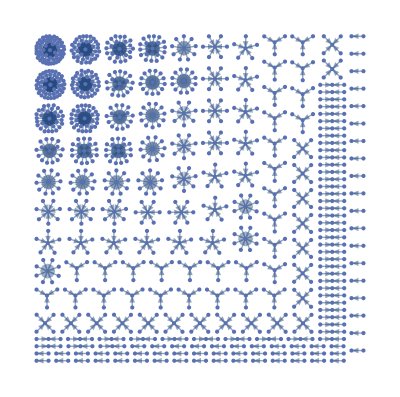

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","BasePhysicalQuantity"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by  SI unit:

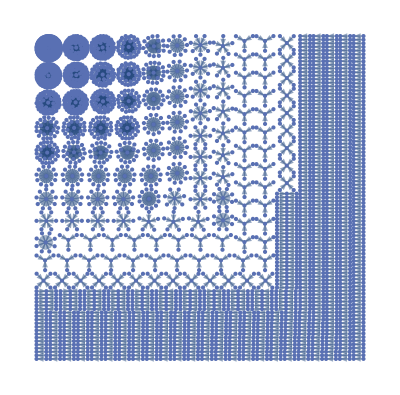

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

There is a difference between the SI unit and the base SI unit. There is only one coherent SI unit for a physical quantity, but conventionally different combinations of SI units that are dimensionally equivalent may be used for different quantities.

I can find all the physical quantities with power.

```mathematica
PhysicalQuantityLookup[Quantity[1, "Watts"]]
```

{power,energy flux,electric power,energy flow rate,heat flow rate,real power,active power,battery energy self-discharge rate,bolometric luminosity,tonnage rating,dietary energy intake rate,electric apparent power,electric complex power,electric non-active power,electric reactive power,energy consumption rate,energy production rate,input power,Larmor power,livestock carrying capacity,luminosity,mechanical power,output power,radiant power,solar panel electric output power,solar power,sound power,stellar luminosity,tidal power,vacuum pump leakage rate,wave power,wind power}

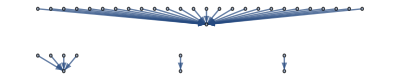

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityLookup[Quantity[1, "Watts"]],EntityValue[PhysicalQuantityLookup[Quantity[1, "Watts"]],EntityProperty["PhysicalQuantity","SIUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

```mathematica
Entity["PhysicalQuantity","VacuumPumpLeakageRate"]["SIUnit"]
```

1 L Pa/s

Group by SI base unit:

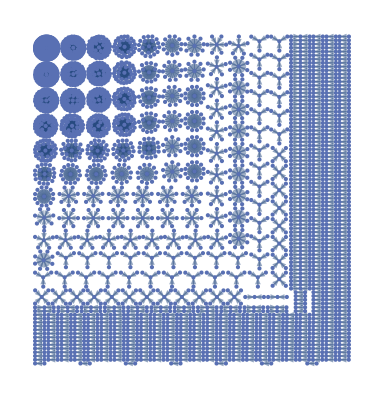

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],EntityValue[PhysicalQuantityData[],EntityProperty["PhysicalQuantity","SIBaseUnit"]]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by total absolute dimension:

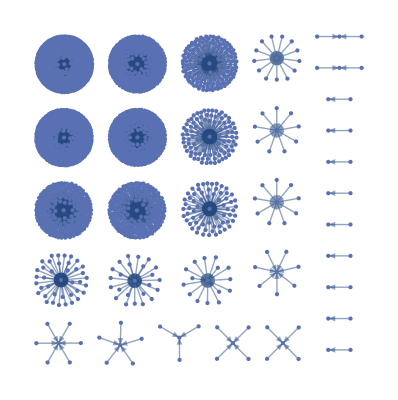

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],Total[Abs[#[[All,-1]]]]&/@EntityValue[PhysicalQuantityData[],"Dimensions"]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Group by total dimensions:

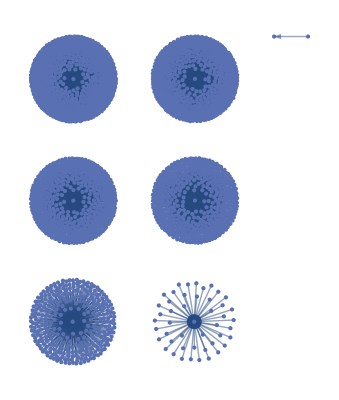

```mathematica
Graph[Rule@@@DeleteCases[Transpose[{PhysicalQuantityData[],Length/@EntityValue[PhysicalQuantityData[],"Dimensions"]}],{_,_Missing}],VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

This comes from a neat example for the documentation for PhysicalQuantity.

Visualize the dimensionality of physical quantities based on the standard dimensions:

```mathematica
dimensions={"LengthUnit","TimeUnit","AngleUnit","MassUnit","PhotonUnit","TemperatureDifferenceUnit","AmountUnit","TemperatureUnit","ElectricCurrentUnit","LuminousIntensityUnit","InformationUnit"};
```

Collect all physical quantities containing only those dimensions:

```mathematica
DimensionData=EntityValue[EntityClass["PhysicalQuantity","Dimensions"->(ContainsOnly[#[[All,1]],dimensions]&)],{"CanonicalName","Dimensions"}];
```

Convert dimension lists to vectors:

```mathematica
DimensionVector//ClearAll
DimensionVector[dims_]:=Lookup[Rule@@@dims,#,0]&/@dimensions
```

Visualize as a feature space plot:

```mathematica
FeatureSpacePlot[Callout[DimensionVector[#2],#1]&@@@DimensionData,LabelingFunction->None,ImageSize->Full]
```

-Graphics-

## Formula Data examples

Find all formulas that contain both the speed of light and Planck's constant as parameters:

```mathematica
Grid[{#,FormulaData[#]}&/@Select[FormulaData[],MemberQ[FormulaData[#],"SpeedOfLight",∞]&&MemberQ[FormulaData[#],"PlanckConstant",∞]&],Dividers->Center,Alignment->Left]
```

ComptonWavelength | λ_C Wavelength==(h/c)/(m Mass)
{BraggsLaw,Energy} | {n MultiplicativeConstants λ Wavelength==2 d Distance Sin[θ Angle],λ Wavelength==(h c)/(E Energy)}
{ComptonShift,Wavelengths} | -λ Wavelength+λ' LightWavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{ComptonShift,WavelengthShift} | Δλ Wavelength==((1-Cos[θ Angle]) ( h/c))/(m Mass)
{PhotonEnergy,Wavelength} | E Energy==(h c)/(λ Wavelength)
{PhotonMomentum,Frequency} | p Momentum==( h/c) ν Frequency
{PhotonWavelength,Energy} | E Energy==(h c)/(λ Wavelength)
{PlanckRadiationLaw,Frequency} | L[ν] RadioBrightness==((2 h/c^2) (ν Frequency)^3)/(-1+ⅇ^((( h/k) ν Frequency)/(T Temperature)))
{PlanckRadiationLaw,Wavelength} | L[λ] SpectralRadianceWithRespectToWavelength==(2 h c^2)/((-1+ⅇ^((h c/k)/(T Temperature λ Wavelength))) (λ Wavelength)^5)
{ThermalDeBroglieWavelength,MasslessParticle} | Λ Wavelength==(1/(2 π^(1/3)) h c/k)/(T Temperature)
{DeBroglieRelationsRelativistic,Frequency,Momentum} | f Frequency==(1 /h) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2))
{DeBroglieRelationsRelativistic,Frequency,Velocity} | f Frequency==(( c^2/h) m Mass)/(√(1+(-1 /c^2) (v Speed)^2))
{DeBroglieRelationsRelativistic,Wavelength,KineticEnergy} | λ Wavelength==(h c)/(√((K Energy)^2+(2 c^2) K Energy m Mass))
{DeBroglieRelationsRelativistic,Wavelength,Velocity} | λ Wavelength==(( h) √(1+(-1 /c^2) (v Speed)^2))/(m Mass v Speed)

I am including a neat example of exploring fundamental physics formulas:

Select all formulas that contain Planck's constant, speed of light, or gravitational constant as a parameter:

```mathematica
chGFormulas = Select[(Column[Flatten@{#, FormulaData[#],FormulaData[#,"QuantityVariableTable"]}]& /@ FormulaData[]) /. 
Quantity[q_,"ReducedPlanckConstant"]:> Quantity[q/.None->1/(2Pi),"PlanckConstant"],        
                                           MemberQ[#, "PlanckConstant"|"SpeedOfLight"|"GravitationalConstant", ∞]&];
```

Construct a network of formulas based on related physical quantities:

```mathematica
chGformulaNetwork = Select[{UndirectedEdge[#1,#2],Length[Intersection @@(Union[Last/@Cases[#,_QuantityVariable, ∞]]& /@ {#1, #2})]}&@@@ Subsets[chGFormulas, {2}],Last[#]>0&];
```

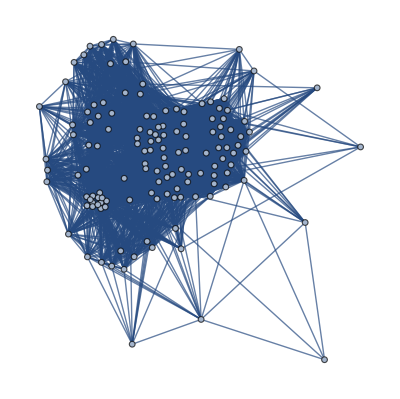

```mathematica
Graph[First /@ chGformulaNetwork,EdgeWeight->1/(Last /@ chGformulaNetwork),
       GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},
       VertexLabels->Placed["Name",Tooltip],ImageSize->Full]
```

Analyze the structure of the graph:

```mathematica
CommunityGraphPlot[Graph[First /@ chGformulaNetwork,EdgeWeight->1/(Last /@ chGformulaNetwork),
       GraphLayout->{"VertexLayout"->{"SpringElectricalEmbedding","EdgeWeighted"->True}},
       VertexLabels->Placed["Name",Tooltip],ImageSize->Full]]
```

-Graphics-

## NondimensionalizationTransform examples

Transform Coulomb's law and Newton's law of gravitation using different sets of natural units:

```mathematica
naturalunits={"PlanckUnits","HartreeAtomicUnits","RydbergAtomicUnits","LorentzHeavisideNaturalUnits","GaussianNaturalUnits"};
```

```mathematica
cleq=First@FormulaData["CoulombsLaw"]
```

F Force==((1/(4 π) /ε_0) Q_1 ElectricCharge Q_2 ElectricCharge)/(r Distance)^2

```mathematica
nlogeq=FormulaData["NewtonsLawOfUniversalGravitation"]
```

F Force==(( G) m_1 Mass m_2 Mass)/(r Distance)^2

```mathematica
coulomb=NondimensionalizationTransform[cleq,{"F" "Force",Subscript["Q", 1] "ElectricCharge", Subscript["Q", 2] "ElectricCharge","r" "Distance"},{f,q1,q2,ρ},UnitSystem->#]&/@naturalunits;
gravity=NondimensionalizationTransform[nlogeq,{"F" "Force", Subscript["m", 1] "Mass", Subscript["m", 2] "Mass","r" "Distance"},{f,m1,m2,ρ},UnitSystem->#]&/@naturalunits;
```

Compare how the formulas look under different natural unit systems:

```mathematica
Grid[Prepend[Transpose[{naturalunits,gravity,coulomb}],{"unit system","gravitational force","electrostatic force"}],Dividers->Center]
```

unit system | gravitational force | electrostatic force
PlanckUnits | f==(m1 m2)/ρ^2 | f==(q1 q2)/ρ^2
HartreeAtomicUnits | f (1/(4 π) e^2/(m_e^2 ε_0 G))==(m1 m2)/ρ^2 | f==(q1 q2)/ρ^2
RydbergAtomicUnits | f (1/(8 π) e^2/(m_e^2 ε_0 G))==(m1 m2)/ρ^2 | 1024 f==(q1 q2)/ρ^2
LorentzHeavisideNaturalUnits | 1.491×10^56 f==(m1 m2)/ρ^2 | f (16 π^2 α ε_0 ℏ c/e^2)==(q1 q2)/ρ^2
GaussianNaturalUnits | 1.491×10^56 f==(m1 m2)/ρ^2 | f (4 π α ε_0 ℏ c/e^2)==(q1 q2)/ρ^2

## Physical Constant examples

Visualize the characteristic length and mass scales for various objects (cf. https://arxiv.org/pdf/1910.00481https://arxiv.org/pdf/1910.00481):

```mathematica
data={
"universe"->{"UniverseRadius","UniverseMass"},
"Planck"->{"PlanckLength","PlanckMass"},
"CQ point"->{"CosmologicalQuantumPointLength","CosmologicalQuantumPointMass"},
"Earth"->{"EarthMeanRadius","EarthMass"},
"Sun"->{"SolarRadius","SolarMass"},
"electron"->{"ClassicalElectronRadius","ElectronMass"},
"proton"->{"ClassicalProtonRadius","ProtonMass"}
};
```

Compute the common logarithms for the magnitudes of the preceding length/radius pairs:

```mathematica
pts=Append[Map[Log10[QuantityMagnitude[UnitConvert[Entity["PhysicalConstant",#]["Value"],"SIBase"]]]&,data[[All,2]],{2}],{0,0}];
```

```mathematica
labels=Append[data[[All,1]],"human"];
```

Plot the points in length-mass space. where the red line marks the quantum mechanical boundary, the green line marks the black hole boundary, the light blue line marks the boundary from the cosmological density, and the point of intersection of the black hole and cosmological lines is termed the cosmological-quantum (CQ) point:

```mathematica
Show[{
Graphics[{AbsoluteThickness[2],Transpose[{{Green,Hue[.5],Red},InfiniteLine/@Subsets[Take[pts,3],{2}]}]
}],
ListPlot[Thread[pts->labels],]
},]
```

-Graphics-

## Dimensional Combinations examples

Explore the possible dimensionless combinations of electromagnetic physical quantities:

```mathematica
DimensionalCombinations[{
  QuantityVariable["Q", "ElectricCharge"],
  QuantityVariable["V", "ElectricPotential"], QuantityVariable["I", "ElectricCurrent"], QuantityVariable["R", "ElectricResistance"],
  QuantityVariable["C", "ElectricCapacitance"], QuantityVariable["L", "MagneticInductance"],
  QuantityVariable["M", "MagneticMemristance"], QuantityVariable["Φ", "MagneticFlux"]},
 GeneratedParameters -> None]
```

{(M MagneticMemristance)/(R ElectricResistance),(Q ElectricCharge)/(C ElectricCapacitance V ElectricPotential),(Φ MagneticFlux)/(Q ElectricCharge R ElectricResistance),(Φ MagneticFlux)/(M MagneticMemristance Q ElectricCharge),(I ElectricCurrent R ElectricResistance)/(V ElectricPotential),(I ElectricCurrent M MagneticMemristance)/(V ElectricPotential),(Φ MagneticFlux)/(I ElectricCurrent L MagneticInductance),(L MagneticInductance)/(C ElectricCapacitance (R ElectricResistance)^2),(C ElectricCapacitance (M MagneticMemristance)^2)/(L MagneticInductance),((I ElectricCurrent)^2 L MagneticInductance)/(Q ElectricCharge V ElectricPotential),(I ElectricCurrent Φ MagneticFlux)/(Q ElectricCharge V ElectricPotential),(L MagneticInductance V ElectricPotential)/(Q ElectricCharge (R ElectricResistance)^2),((M MagneticMemristance)^2 Q ElectricCharge)/(L MagneticInductance V ElectricPotential),(Φ MagneticFlux)^2/(L MagneticInductance Q ElectricCharge V ElectricPotential),(C ElectricCapacitance I ElectricCurrent R ElectricResistance)/(Q ElectricCharge),(I ElectricCurrent L MagneticInductance)/(Q ElectricCharge R ElectricResistance),(C ElectricCapacitance (I ElectricCurrent)^2 L MagneticInductance)/(Q ElectricCharge)^2,(C ElectricCapacitance I ElectricCurrent M MagneticMemristance)/(Q ElectricCharge),(C ElectricCapacitance I ElectricCurrent Φ MagneticFlux)/(Q ElectricCharge)^2,(I ElectricCurrent L MagneticInductance)/(M MagneticMemristance Q ElectricCharge),(C ElectricCapacitance (Φ MagneticFlux)^2)/(L MagneticInductance (Q ElectricCharge)^2),((I ElectricCurrent)^2 L MagneticInductance)/(C ElectricCapacitance (V ElectricPotential)^2),(I ElectricCurrent Φ MagneticFlux)/(C ElectricCapacitance (V ElectricPotential)^2),(Φ MagneticFlux)/(C ElectricCapacitance R ElectricResistance V ElectricPotential),(R ElectricResistance Φ MagneticFlux)/(L MagneticInductance V ElectricPotential),(Φ MagneticFlux)^2/(C ElectricCapacitance L MagneticInductance (V ElectricPotential)^2),(Φ MagneticFlux)/(C ElectricCapacitance M MagneticMemristance V ElectricPotential),(M MagneticMemristance Φ MagneticFlux)/(L MagneticInductance V ElectricPotential),(C ElectricCapacitance I ElectricCurrent (R ElectricResistance)^2)/(Φ MagneticFlux),(C ElectricCapacitance I ElectricCurrent (M MagneticMemristance)^2)/(Φ MagneticFlux)}

Derive the factor for the fine structure constant from physical quantities:

```mathematica
sol=DimensionalCombinations[{},
 IncludeQuantities -> {
  Quantity["SpeedOfLight"], Quantity["PlanckConstant"] , Quantity["ElectricConstant"] ,
  Quantity["ElementaryCharge"]
  },
 GeneratedParameters -> None]
```

{1 ε_0 h c/e^2}

```mathematica
UnitConvert[sol[[1]],"SIBase"]^2/Quantity["FineStructureConstant"]
```

4694.71626 /α

## Using formula Lookup

```mathematica
FormulaLookup["Density"]
```

{MassDensity,Sensitivity,Viscosity,CohensD,JohnsonNyquistNoisePowerSpectralDensity,MagneticEnergyDensity,MassDensity,MolarityDensityConversion,UniformDensitySphereGravitationalBindingEnergy,{BarometricFormula,MassDensity},{BoseCondensationTemperature,NumberDensity},{FermiEnergy,NumberDensity},{IdealGasLaw,Density},{IdealGasSpeedOfSoundPressure,Density},{PixelConverter,PixelDensity},{PixelConverter,StandardPixelDensity},{TransformerUniversalEMF,CrossSectionFluxDensity},{WindPressure,AirDensity},{BarometricFormula,MassDensity,GravitationalAcceleration},{HeatTransferEquation,TemperatureDifference,Density},{MeanFreePath,ElectronDensity,Diameter},{MeanFreePath,ElectronDensity,Radius},{HeatTransferEquation,InitialTemperature,FinalTemperature,Density}}

```mathematica
First[FormulaLookup["Density"]]
```

MassDensity

```mathematica
FormulaData["Properties"]
```

{Classes,ExternalIdentifiers,Formula,QuantityVariableDimensions,QuantityVariableNames,QuantityVariablePhysicalQuantities,QuantityVariables,QuantityVariableTable}

```mathematica
AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→{ρ MassDensity→MassDensity,M Mass→Mass,V Volume→Volume},QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
FormulaData["MassDensity","QuantityVariables"]
```

{ρ MassDensity,M Mass,V Volume}

```mathematica
CanonicalDimensionalProduct/@FormulaData["MassDensity","QuantityVariables"]
```

{L^-3M^1,M^1,L^3}

```mathematica
CanonicalDimensionalProduct[QuantityVariableCanonicalUnit[#]]&/@FormulaData["MassDensity","QuantityVariables"]
```

{CanonicalDimensionalProduct[Kilograms/Meters^3],CanonicalDimensionalProduct[Kilograms],CanonicalDimensionalProduct[Meters^3]}

```mathematica
QuantityVariableDimensions["ρ" "MassDensity"]
```

{{LengthUnit,-3},{MassUnit,1}}

```mathematica
CanonicalDimensionalProduct[QuantityVariableDimensions["ρ" "MassDensity"]]
```

CanonicalDimensionalProduct[{{LengthUnit,-3},{MassUnit,1}}]

```mathematica
UnitDimensions["ρ" "MassDensity"]
```

UnitDimensions[ρ MassDensity]

```mathematica
CanonicalDimensionalProduct[#]&/@FormulaData["MassDensity","QuantityVariables"]
```

{L^-3M^1,M^1,L^3}

```mathematica
CanonicalDimensionalProduct/@
```

```mathematica
FormulaData["MassDensity","QuantityVariablePhysicalQuantities"]
```

{ρ MassDensity→MassDensity,M Mass→Mass,V Volume→Volume}

```mathematica
Association[FormulaData["MassDensity","QuantityVariablePhysicalQuantities"]]
```

<|ρ MassDensity→MassDensity,M Mass→Mass,V Volume→Volume|>

```mathematica
Function[p,Entity["PhysicalQuantity",p]]/@Association[FormulaData["MassDensity","QuantityVariablePhysicalQuantities"]]
```

<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>

```mathematica
<|"ρ" "MassDensity"->Entity["PhysicalQuantity","MassDensity"],"M" "Mass"->Entity["PhysicalQuantity","Mass"],"V" "Volume"->Entity["PhysicalQuantity","Volume"]|>
```

<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>

```mathematica
Entity["PhysicalQuantity","MassDensity"]
```

Entity[PhysicalQuantity,MassDensity]

```mathematica
Function[p,Entity["PhysicalQuantity",p]]/@<|"ρ" "MassDensity"->"MassDensity","M" "Mass"->"Mass","V" "Volume"->"Volume"|>
```

<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>

```mathematica
<|"ρ" "MassDensity"->Entity["PhysicalQuantity","MassDensity"],"M" "Mass"->Entity["PhysicalQuantity","Mass"],"V" "Volume"->Entity["PhysicalQuantity","Volume"]|>
```

```mathematica
AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→{ρ MassDensity→MassDensity,M Mass→Mass,V Volume→Volume},QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>,QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
MatchQ[{p->q},{p_->q_}]
```

True

```mathematica
MatchQ[{p->q},{Repeated[p_->q_]}]
```

True

```mathematica
MatchQ[{p->q,r->s},{Repeated[_->_]}]
```

True

```mathematica
MatchQ[{p->q,r},{Repeated[_->_]}]
```

False

```mathematica
Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]
```

<|QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume}|>

```mathematica
Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]
```

<|QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→{ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]}|>

```mathematica
Keys[Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]]
```

{QuantityVariableDimensions,QuantityVariableNames,QuantityVariablePhysicalQuantities}

```mathematica
List[Key[#]]&/@Keys[Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]]
```

{{Key[QuantityVariableDimensions]},{Key[QuantityVariableNames]},{Key[QuantityVariablePhysicalQuantities]}}

```mathematica
MapAt[Association,Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]],List[Key[#]]&/@Keys[Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]]]
```

<|QuantityVariableDimensions→<|ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}|>,QuantityVariableNames→<|ρ MassDensity→mass density,M Mass→mass,V Volume→volume|>,QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>|>

```mathematica
Names["Association*"]
```

{Association,AssociationFormat,AssociationMap,AssociationQ,AssociationThread}

```mathematica
Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]
```

<|QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→{ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]}|>

```mathematica
Association@KeyValueMap[#1->Association[#2]&,Select[MatchQ[#,{Repeated[_->_]}]&][MapAt[Normal[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]]&,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],Key["QuantityVariablePhysicalQuantities"]]]]
```

<|QuantityVariableDimensions→<|ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}|>,QuantityVariableNames→<|ρ MassDensity→mass density,M Mass→mass,V Volume→volume|>,QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>|>

```mathematica
ResourceFunction["MapCases"][Association,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],{Repeated[_->_]}]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→<|ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}|>,QuantityVariableNames→<|ρ MassDensity→mass density,M Mass→mass,V Volume→volume|>,QuantityVariablePhysicalQuantities→<|ρ MassDensity→MassDensity,M Mass→Mass,V Volume→Volume|>,QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
Dataset[ResourceFunction["MapCases"][Association,AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]],{Repeated[_->_]}]]
```

```mathematica
MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→{ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}},QuantityVariableNames→{ρ MassDensity→mass density,M Mass→mass,V Volume→volume},QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>,QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→<|ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}|>,QuantityVariableNames→<|ρ MassDensity→mass density,M Mass→mass,V Volume→volume|>,QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>,QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3}|>

```mathematica
CanonicalDimensionalProduct/@ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]]["QuantityVariablePhysicalQuantities"]
```

<|ρ MassDensity→L^-3M^1,M Mass→M^1,V Volume→L^3|>

```mathematica
<|"QuantityVariableCanonicalDimensionalProducts"->CanonicalDimensionalProduct/@ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]]["QuantityVariablePhysicalQuantities"]|>
```

<|QuantityVariableCanonicalDimensionalProducts→<|ρ MassDensity→L^-3M^1,M Mass→M^1,V Volume→L^3|>|>

```mathematica
Join[ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]],<|"QuantityVariableCanonicalDimensionalProducts"->CanonicalDimensionalProduct/@ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]]["QuantityVariablePhysicalQuantities"]|>]
```

<|Classes→{Chemistry,Physics,{Chemistry,Liquids},{Physics,Mechanics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q29539,<|Label→density,Description→mass per volume|>]Wikidatadensityhttp://www.wikidata.org/entity/Q29539},Formula→ρ MassDensity==(M Mass)/(V Volume),QuantityVariableDimensions→<|ρ MassDensity→{{LengthUnit,-3},{MassUnit,1}},M Mass→{MassUnit,1},V Volume→{LengthUnit,3}|>,QuantityVariableNames→<|ρ MassDensity→mass density,M Mass→mass,V Volume→volume|>,QuantityVariablePhysicalQuantities→<|ρ MassDensity→Entity[PhysicalQuantity,MassDensity],M Mass→Entity[PhysicalQuantity,Mass],V Volume→Entity[PhysicalQuantity,Volume]|>,QuantityVariables→{ρ MassDensity,M Mass,V Volume},QuantityVariableTable→symbol | description | physical quantity | dimensions
ρ | mass density | MassDensity | {{LengthUnit,-3},{MassUnit,1}}
M | mass | Mass | {MassUnit,1}
V | volume | Volume | {LengthUnit,3},QuantityVariableCanonicalDimensionalProducts→<|ρ MassDensity→L^-3M^1,M Mass→M^1,V Volume→L^3|>|>

```mathematica
Dataset[Join[ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]],<|"QuantityVariableCanonicalDimensionalProducts"->CanonicalDimensionalProduct/@ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData["MassDensity",#]&,FormulaData["Properties"]]]]["QuantityVariablePhysicalQuantities"]|>]]
```

```mathematica
FormulaDataset//ClearAll
FormulaDataset[eq_]:=Dataset[Join[ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData[eq,#]&,FormulaData["Properties"]]]],<|"QuantityVariableCanonicalDimensionalProducts"->CanonicalDimensionalProduct/@ResourceFunction["MapCases"][Association,{Repeated[_->_]}][MapAt[Function[p,Entity["PhysicalQuantity",p]]/@Association[#]&,Key["QuantityVariablePhysicalQuantities"]][AssociationMap[FormulaData[eq,#]&,FormulaData["Properties"]]]]["QuantityVariablePhysicalQuantities"]|>]]
```

```mathematica
FormulaLookup["Density"]
```

{MassDensity,Sensitivity,Viscosity,CohensD,JohnsonNyquistNoisePowerSpectralDensity,MagneticEnergyDensity,MassDensity,MolarityDensityConversion,UniformDensitySphereGravitationalBindingEnergy,{BarometricFormula,MassDensity},{BoseCondensationTemperature,NumberDensity},{FermiEnergy,NumberDensity},{IdealGasLaw,Density},{IdealGasSpeedOfSoundPressure,Density},{PixelConverter,PixelDensity},{PixelConverter,StandardPixelDensity},{TransformerUniversalEMF,CrossSectionFluxDensity},{WindPressure,AirDensity},{BarometricFormula,MassDensity,GravitationalAcceleration},{HeatTransferEquation,TemperatureDifference,Density},{MeanFreePath,ElectronDensity,Diameter},{MeanFreePath,ElectronDensity,Radius},{HeatTransferEquation,InitialTemperature,FinalTemperature,Density}}

```mathematica
FormulaDataset["Sensitivity"]
```

```mathematica
Normal@FormulaDataset["Sensitivity"]
```

<|Classes→{Health&Medicine,Mathematics,{Health&Medicine,Medicine},{Mathematics,Statistics}},ExternalIdentifiers→{ExternalIdentifier[WikidataID,Q3808900,<|Label→sensitivity and specificity,Description→statistical measures of the performance of a binary classification test|>]Wikidatasensitivity and specificityhttp://www.wikidata.org/entity/Q3808900},Formula→sens MultiplicativeConstants==(tp MultiplicativeConstants)/(fn MultiplicativeConstants+tp MultiplicativeConstants),QuantityVariableDimensions→<|sens MultiplicativeConstants→Dimensionless,tp MultiplicativeConstants→Dimensionless,fn MultiplicativeConstants→Dimensionless|>,QuantityVariableNames→<|sens MultiplicativeConstants→sensitivity,tp MultiplicativeConstants→true positives,fn MultiplicativeConstants→false negatives|>,QuantityVariablePhysicalQuantities→<|sens MultiplicativeConstants→Entity[PhysicalQuantity,MultiplicativeConstants],tp MultiplicativeConstants→Entity[PhysicalQuantity,MultiplicativeConstants],fn MultiplicativeConstants→Entity[PhysicalQuantity,MultiplicativeConstants]|>,QuantityVariables→{sens MultiplicativeConstants,tp MultiplicativeConstants,fn MultiplicativeConstants},QuantityVariableTable→symbol | description | physical quantity | dimensions
sens | sensitivity | MultiplicativeConstants | Dimensionless
tp | true positives | MultiplicativeConstants | Dimensionless
fn | false negatives | MultiplicativeConstants | Dimensionless,QuantityVariableCanonicalDimensionalProducts→<|sens MultiplicativeConstants→Null,tp MultiplicativeConstants→Null,fn MultiplicativeConstants→Null|>|>

```mathematica
FormulaDataset["Viscosity"]
```

```mathematica
QuantityVariableDimensions[QuantityVariable["sens","MultiplicativeConstants"]]
```

{}

```mathematica
QuantityVariableDimensions[QuantityVariable["sens","MultiplicativeConstants"]]!={}&&ContainsAll[{"TimeUnit",
"LengthUnit","MassUnit",
"ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit",
"AngleUnit","InformationUnit",
"MoneyUnit","PersonUnit","SolidAngleUnit","TemperatureDifferenceUnit","PhotonUnit"},
First[Transpose[QuantityVariableDimensions[QuantityVariable["sens","MultiplicativeConstants"]]]]]
```

False

```mathematica
CanonicalDimensionalProduct[QuantityVariable["sens","MultiplicativeConstants"]]
```

1

Some quantities are dimensionless.

```mathematica
Quantity["Exa"]
```

1 E

```mathematica
UnitDimensions[Quantity[1, "Exa"]]
```

{}

```mathematica
UnitDimensions[Quantity[1, "Exa"]]!={}&&ContainsAll[{"TimeUnit",
"LengthUnit","MassUnit",
"ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit",
"AngleUnit","InformationUnit",
"MoneyUnit","PersonUnit","SolidAngleUnit","TemperatureDifferenceUnit","PhotonUnit"},
First[Transpose[UnitDimensions[Quantity[1, "Exa"]]]]]
```

False

```mathematica
CanonicalDimensionalProduct[Quantity[1, "Exa"]]
```

1

```mathematica
dimensions={"LengthUnit","TimeUnit","AngleUnit","MassUnit","PhotonUnit","TemperatureDifferenceUnit","AmountUnit","TemperatureUnit","ElectricCurrentUnit","LuminousIntensityUnit","InformationUnit"};
```

```mathematica
photonClass=EntityList@EntityClass["PhysicalQuantity","Dimensions"->(ContainsAll[#[[All,1]],{"PhotonUnit"}]&)]
```

{absorption cross section,chemiluminescence yield,cross section per photon,energy per photon,photometer quantum sensitivity,photon cost,photon count,photon count exposure,photon count spectral irradiance,photon energy flux,photon exitance,photon exposure,photon flux,photon intensity,photon irradiance,photon illuminance,photon number density,photon pointance,photon radiance,photon per energy,spectral photon count flux,two-photon absorption cross section,two-photon absorption/emission coefficient,X-ray brilliance}

```mathematica
photonData=EntityValue[EntityClass["PhysicalQuantity","Dimensions"->(ContainsAll[#[[All,1]],{"PhotonUnit"}]&)],{"CanonicalName","Dimensions"}]
```

{{AbsorptionCrossSection,{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{ChemiluminescenceYield,{{AmountUnit,-1},{PhotonUnit,1}}},{CrossSectionPerPhoton,{{LengthUnit,2},{PhotonUnit,-1}}},{EnergyPerPhoton,{{LengthUnit,2},{MassUnit,1},{PhotonUnit,-1},{TimeUnit,-2}}},{PhotometerQuantumSensitivity,{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonCost,{{MoneyUnit,1},{PhotonUnit,-1}}},{PhotonCount,{{PhotonUnit,1}}},{PhotonCountExposure,{{LengthUnit,-2},{PhotonUnit,1}}},{PhotonCountSpectralIrradiance,{{LengthUnit,-3},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonEnergyFlux,{{LengthUnit,2},{MassUnit,1},{PhotonUnit,-1},{TimeUnit,-3}}},{PhotonExitance,{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonExposure,{{LengthUnit,-2},{PhotonUnit,1}}},{PhotonFlux,{{PhotonUnit,1},{TimeUnit,-1}}},{PhotonIntensity,{{AngleUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonIrradiance,{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonLuminance,{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonNumberDensity,{{LengthUnit,-3},{PhotonUnit,1}}},{PhotonPointance,{{AngleUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonRadiance,{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}}},{PhotonsPerEnergy,{{LengthUnit,-2},{MassUnit,-1},{PhotonUnit,1},{TimeUnit,2}}},{SpectralPhotonCountFlux,{{LengthUnit,-3},{PhotonUnit,1},{TimeUnit,-1}}},{TwoPhotonAbsorptionCrossSection,{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}}},{TwoPhotonAbsorptionEmissionCrossSection,{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}}},{XRayBrilliance,{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1}}}}

```mathematica
DimensionVector[dims_]:=Lookup[Rule@@@dims,#,0]&/@dimensions
```

```mathematica
FeatureSpacePlot[Callout[DimensionVector[#2],#1]&@@@photonData,LabelingFunction->None]
```

-Graphics-

```mathematica
Table[CanonicalDimensionalProduct[i],{i,photonClass}]
```

{T^-1L^-2H^1,N^-1H^1,L^2H^-1,T^-2L^2M^1H^-1,T^-1L^-2H^1,C^1H^-1,H^1,L^-2H^1,T^-1L^-3H^1,T^-3L^2M^1H^-1,T^-1L^-2H^1,L^-2H^1,T^-1H^1,T^-1Α^-2H^1,T^-1L^-2H^1,T^-1L^-2Α^-2H^1,L^-3H^1,T^-1Α^-2H^1,T^-1L^-2Α^-2H^1,T^2L^-2M^-1H^1,T^-1L^-3H^1,T^1L^4H^-1,T^1L^4H^-1,L^-2Α^-2H^1}

```mathematica
defaultCanonicalSettings=Association@{"TimeUnit"->"T","AmountUnit"->"N",
"AngleUnit"->"Α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M",
"TemperatureUnit"->"Θ",
"LuminousIntensityUnit"->"J","InformationUnit"->"F","MoneyUnit"->"C",
"PersonUnit"->"P","SolidAngleUnit"->"Φ",
"TemperatureDifferenceUnit"->"D","PhotonUnit"->"H"}
```

<|TimeUnit→T,AmountUnit→N,AngleUnit→Α,ElectricCurrentUnit→I,LengthUnit→L,MassUnit→M,TemperatureUnit→Θ,LuminousIntensityUnit→J,InformationUnit→F,MoneyUnit→C,PersonUnit→P,SolidAngleUnit→Φ,TemperatureDifferenceUnit→D,PhotonUnit→H|>

```mathematica
Join[defaultCanonicalSettings,<|"AngleUnit"->"α"|>]
```

<|TimeUnit→T,AmountUnit→N,AngleUnit→α,ElectricCurrentUnit→I,LengthUnit→L,MassUnit→M,TemperatureUnit→Θ,LuminousIntensityUnit→J,InformationUnit→F,MoneyUnit→C,PersonUnit→P,SolidAngleUnit→Φ,TemperatureDifferenceUnit→D,PhotonUnit→H|>

```mathematica
Keys[Join[defaultCanonicalSettings,<|"AngleUnit"->"α"|>]]
```

{TimeUnit,AmountUnit,AngleUnit,ElectricCurrentUnit,LengthUnit,MassUnit,TemperatureUnit,LuminousIntensityUnit,InformationUnit,MoneyUnit,PersonUnit,SolidAngleUnit,TemperatureDifferenceUnit,PhotonUnit}

```mathematica
CanonicalDimensionalProduct[quantity_?QuantityQ,dimensionSymbols_?AssociationQ]:=Block[{permutation,
quantityDimensions,dimensions,exponents,
permutedDimensions,permutedExponents,SIDimensions,customDimensions,allNecessaryDimensions,joinedDimensionsData},
quantityDimensions=UnitDimensions[quantity];
SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit",
"TemperatureUnit",
"AmountUnit","LuminousIntensityUnit"};

customDimensions=Keys[dimensionSymbols];
joinedDimensionsData=Join[<|"TimeUnit"->"T","AmountUnit"->"N","AngleUnit"->"α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M","TemperatureUnit"->"Θ","LuminousIntensityUnit"->"J"|>,dimensionSymbols];
allNecessaryDimensions=Values[joinedDimensionsData];
dimensions=First[Transpose[quantityDimensions]];{permutation,
quantityDimensions,dimensions,
permutedDimensions,SIDimensions,customDimensions,allNecessaryDimensions,joinedDimensionsData};
Lookup[joinedDimensionsData,dimensions]
(*exponents=Last[Transpose[quantityDimensions]];
permutation=FindPermutation[dimensions,
DeleteElements[allNecessaryDimensions,Complement[allNecessaryDimensions,dimensions]]];
permutedDimensions=Permute[dimensions,permutation];
permutedExponents=Permute[exponents,permutation];
Row[Superscript@@@(Transpose[{permutedDimensions,
permutedExponents}]/. Thread[Normal[dimensionSymbols]])*)]/;UnitDimensions[quantity]!={}&&ContainsAll[Keys[dimensionSymbols],
First[Transpose[UnitDimensions[quantity]]]]
```

```mathematica
CanonicalDimensionalProduct[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"],]
```

```mathematica
differentDimensionalSymbolSettings=Join[defaultCanonicalSettings,<|"PhotonUnit"->"𝔓"|>]
```

<|TimeUnit→T,AmountUnit→N,AngleUnit→Α,ElectricCurrentUnit→I,LengthUnit→L,MassUnit→M,TemperatureUnit→Θ,LuminousIntensityUnit→J,InformationUnit→F,MoneyUnit→C,PersonUnit→P,SolidAngleUnit→Φ,TemperatureDifferenceUnit→D,PhotonUnit→𝔓|>

```mathematica
CanonicalDimensionalProduct[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"],<|"TimeUnit"->"T","AmountUnit"->"N","AngleUnit"->"Α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M","TemperatureUnit"->"Θ","LuminousIntensityUnit"->"J","InformationUnit"->"F","MoneyUnit"->"C","PersonUnit"->"P","SolidAngleUnit"->"Φ","TemperatureDifferenceUnit"->"D","PhotonUnit"->"𝔓"|>]
```

{L,𝔓,T}

```mathematica
Values[<|"TimeUnit"->"T","AmountUnit"->"N","AngleUnit"->"Α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M","TemperatureUnit"->"Θ","LuminousIntensityUnit"->"J","InformationUnit"->"F","MoneyUnit"->"C","PersonUnit"->"P","SolidAngleUnit"->"Φ","TemperatureDifferenceUnit"->"D","PhotonUnit"->"𝔓"|>]
```

{T,N,Α,I,L,M,Θ,J,F,C,P,Φ,D,𝔓}

```mathematica
UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]
```

{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}}

```mathematica
defaultCanonicalSettings
```

<|TimeUnit→T,AmountUnit→N,AngleUnit→Α,ElectricCurrentUnit→I,LengthUnit→L,MassUnit→M,TemperatureUnit→Θ,LuminousIntensityUnit→J,InformationUnit→F,MoneyUnit→C,PersonUnit→P,SolidAngleUnit→Φ,TemperatureDifferenceUnit→D,PhotonUnit→H|>

```mathematica
defaultCanonicalSettings["TimeUnit"]
```

T

```mathematica
FindPermutation[{{"LengthUnit",4},{"PhotonUnit",-1},{"TimeUnit",1}},{{"TimeUnit",1},{"LengthUnit",4},{"PhotonUnit",-1}}]
```

Cycles[{{1,2,3}}]

```mathematica
Permute[{{"LengthUnit",4},{"PhotonUnit",-1},{"TimeUnit",1}},FindPermutation[{{"LengthUnit",4},{"PhotonUnit",-1},{"TimeUnit",1}},{{"TimeUnit",1},{"LengthUnit",4},{"PhotonUnit",-1}}]]
```

{{TimeUnit,1},{LengthUnit,4},{PhotonUnit,-1}}

```mathematica
Keys[defaultCanonicalSettings]
```

{TimeUnit,AmountUnit,AngleUnit,ElectricCurrentUnit,LengthUnit,MassUnit,TemperatureUnit,LuminousIntensityUnit,InformationUnit,MoneyUnit,PersonUnit,SolidAngleUnit,TemperatureDifferenceUnit,PhotonUnit}

```mathematica
UniqueElements[{Keys[defaultCanonicalSettings],{"TimeUnit"}}]
```

{{AmountUnit,AngleUnit,ElectricCurrentUnit,LengthUnit,MassUnit,TemperatureUnit,LuminousIntensityUnit,InformationUnit,MoneyUnit,PersonUnit,SolidAngleUnit,TemperatureDifferenceUnit,PhotonUnit},{}}

```mathematica
Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]
```

{{LengthUnit,PhotonUnit,TimeUnit},{4,-1,1}}

```mathematica
First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]
```

{LengthUnit,PhotonUnit,TimeUnit}

```mathematica
Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]
```

{LengthUnit,PhotonUnit,TimeUnit}

```mathematica
Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]
```

{AmountUnit,AngleUnit,ElectricCurrentUnit,InformationUnit,LuminousIntensityUnit,MassUnit,MoneyUnit,PersonUnit,SolidAngleUnit,TemperatureDifferenceUnit,TemperatureUnit}

```mathematica
DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]
```

{TimeUnit,LengthUnit,PhotonUnit}

```mathematica
FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]
```

Cycles[{{1,2,3}}]

```mathematica
Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]
```

{TimeUnit,LengthUnit,PhotonUnit}

```mathematica
{Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]],}
```

```mathematica
Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]
```

{1,4,-1}

```mathematica
{Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}
```

{{TimeUnit,LengthUnit,PhotonUnit},{1,4,-1}}

```mathematica
Transpose[{Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}]
```

{{TimeUnit,1},{LengthUnit,4},{PhotonUnit,-1}}

```mathematica
Lookup[differentDimensionalSymbolSettings,"TimeUnit"]
```

T

```mathematica
Lookup[differentDimensionalSymbolSettings,Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]]
```

{T,L,𝔓}

```mathematica
{Lookup[differentDimensionalSymbolSettings,Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}
```

{{T,L,𝔓},{1,4,-1}}

```mathematica
Transpose[{Lookup[differentDimensionalSymbolSettings,Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}]
```

{{T,1},{L,4},{𝔓,-1}}

```mathematica
Row[Superscript@@@(Transpose[{Lookup[differentDimensionalSymbolSettings,Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}])]
```

T^1L^4𝔓^-1

```mathematica
Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]//UnitDimensions
```

{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}}

```mathematica
OrderingBy[]
```

```mathematica
Ordering
```

How do I figure out that I need the order

```mathematica
customCanonicalDimensionalProduct//ClearAll
customCanonicalDimensionalProduct[q_?QuantityQ,association_?AssociationQ]:=
Block[{SICanonicalSettings,lookupAssociation},SICanonicalSettings=<|"TimeUnit"->"T","LengthUnit"->"L","MassUnit"->"M","ElectricCurrentUnit"->"I","TemperatureUnit"->"Θ","AmountUnit"->"N","LuminousIntensityUnit"->"J"|>;lookupAssociation=Join[SICanonicalSettings,association];Row[Superscript@@@(Transpose[{Lookup[lookupAssociation,Permute[First[Transpose[UnitDimensions[q]]],FindPermutation[First[Transpose[UnitDimensions[q]]],DeleteElements[Keys@lookupAssociation,Complement[Keys@lookupAssociation,Intersection[Keys[lookupAssociation],First[Transpose[UnitDimensions[q]]]]]]]]],Permute[Last[Transpose[UnitDimensions[q]]],FindPermutation[First[Transpose[UnitDimensions[q]]],DeleteElements[Keys@lookupAssociation,Complement[Keys@lookupAssociation,Intersection[Keys[lookupAssociation],First[Transpose[UnitDimensions[q]]]]]]]]}])]]
```

```mathematica
customCanonicalDimensionalProduct[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"],differentDimensionalSymbolSettings]
```

T^1L^4𝔓^-1

```mathematica
customCanonicalDimensionalProduct[Entity["PhysicalQuantity","Voltage"]["SIUnit"],<|"ElectricCurrentUnit"->"A"|>]
```

T^-3L^2M^1A^-1

```mathematica
customCanonicalDimensionalProduct[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"],]
```

```mathematica
defaultCanonicalSettings
```

<|TimeUnit→T,AmountUnit→N,AngleUnit→Α,ElectricCurrentUnit→I,LengthUnit→L,MassUnit→M,TemperatureUnit→Θ,LuminousIntensityUnit→J,InformationUnit→F,MoneyUnit→C,PersonUnit→P,SolidAngleUnit→Φ,TemperatureDifferenceUnit→D,PhotonUnit→H|>

```mathematica
<|"TimeUnit"->"T","LengthUnit"->"L","MassUnit"->"M","ElectricCurrentUnit"->"I","TemperatureUnit"->"Θ","AmountUnit"->"N","LuminousIntensityUnit"->"J"|>
```

<|TimeUnit→T,LengthUnit→L,MassUnit→M,ElectricCurrentUnit→I,TemperatureUnit→Θ,AmountUnit→N,LuminousIntensityUnit→J|>

```mathematica
Entity["PhysicalQuantity","PhotometricSensitivity"]["SIUnit"]
```

1 V/(s lx)

```mathematica
customCanonicalDimensionalProduct[Quantity[1, ("Volts")/("Lux" "Seconds")],<|"ElectricCurrentUnit"->"A","LuminousIntensityUnit"->"C","AngleUnit"->"α"|>]
```

T^-4L^4M^1A^-1C^-1α^-2

```mathematica
Keys[<|"TimeUnit"->"T","LengthUnit"->"L","MassUnit"->"M","ElectricCurrentUnit"->"I","TemperatureUnit"->"Θ","AmountUnit"->"N","LuminousIntensityUnit"->"J"|>]
```

{TimeUnit,LengthUnit,MassUnit,ElectricCurrentUnit,TemperatureUnit,AmountUnit,LuminousIntensityUnit}

```mathematica
ContainsOnlySevenBaseDimensions//ClearAll
ContainsOnlySevenBaseDimensions[q_?QuantityQ]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[UnitDimensions[q]]];SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]
ContainsOnlySevenBaseDimensions[q_Entity]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[q["Dimensions"]]];SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]/;EntityTypeName[q]=="PhysicalQuantity"
ContainsOnlySevenBaseDimensions[dimensionsList_]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[dimensionsList]];SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]/;dimensionsList!={}
```

```mathematica
ContainsOnlySevenBaseDimensions[Quantity[1, ("Volts")/("Lux" "Seconds")]]
```

False

```mathematica
ContainsOnlySevenBaseDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]
```

False

```mathematica
ContainsOnlySevenBaseDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]]
```

False

```mathematica
Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["Dimensions"]
```

{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}}

```mathematica
ContainsOnlySevenBaseDimensions[{{"LengthUnit",4},{"PhotonUnit",-1},{"TimeUnit",1}}]
```

False

```mathematica
EntityList@EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)]
```

```mathematica
EntityValue[EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)],"Dimensions"]
```

```mathematica
Function[q,First[Transpose[q["Dimensions"]]]]/@EntityList@EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)]
```

```mathematica
EntityValue[EntityList@EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)],"SIUnit"]
```

```mathematica
Select[!ContainsOnlySevenBaseDimensions[#["Dimensions"]]&][EntityList[EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)]]]
```

{absolute bearing,absorption cross section,absorptivity temperature coefficient,adiabatic heat capacity,adiabatic lapse rate,adiabatic molar heat capacity,adiabatic specific heat capacity,altitude angle,amount of light,plane angle,angle gradient,anglement,angle of attack,angle of deviation,angle of incidence,angle of optical rotation,angle of reflection,angle of refraction,angle of repose,angle of vanishing stability,angle per distance,angle per time magnetic flux density,angular acceleration,angular curvature,angular diameter,angular displacement,angular eccentricity,angular elongation,angular frequency,angular jerk,angular radius,angular radius of curvature,angular resolution,angular resolving power,angular torque,angular velocity,angular wavenumber,Antoine equation constant C,aperture,areal thermal expansion coefficient,area per information,area per person,area per person rate,argument of periapsis,arrival count,arrival rate,artillery piece count,atom count,atom per amount,average bicycle cadence,average heart rate,average population,average run cadence,average swim cadence,average transmission rate,axial tilt,azimuth,back count,bacterium count,bacterium deposition rate,bag count,bagel count,bar count,baryon count,base pair count,basic radiance,batch count,beam emittance,beam jitter,bean count,bearing,beat count,beat rate,amount of berg cryptocurrency,bicycle cadence,bidirectional reflectance distribution function,bidirectional transmittance distribution function,biocapacity,biochemical productivity rate,amount of biologic,bird count,biscuit count,bite count,book page count,bottle count,bowl count,box count,Bragg angle,breast count,Brewster angle,bulb count,bunch count,bun count,bundle count,burpee count,burrito count,business count,business rate,cake count,can count,capon count,carton count,case count,case per person prevalence,cat count,channel capacity,chemiluminescence capacity,chemiluminescence yield,chop count,chromosome count,Class A share count,Class B share count,climate sensitivity,clove count,coating weight,coil turn count,colatitude,coldness,common share count,compass bearing,computing bandwidth,container count,cookie count,cooling degree day,cooling rate,corn dog count,count count,count rate,cracker count,credit count,critical angle,cross section per photon,crunch count,cube count,cup count,cut count,cutlet count,cutoff angular frequency,cyclotron angular frequency,amount of DARK cryptocurrency,dash count,data bandwidth,data packet count,data transfer rate,Debye angular frequency,Debye angular wavenumber,declination,departure count,departure rate,dietary energy supply,differential unidirectional flux,diffraction angle,digital bandwidth,direction and energy distribution of cross section,word count,dog count,dot count,drink count,drop count,dropperful count,drumstick count,refractive index pressure temperature coefficient K1,dynamic viscosity change per temperature difference,ear count,earthquake count,eccentric anomaly,ecological footprint,economic intensity,eel count,effective transmission rate,egg count,egg roll count,egg per mass,Einstein angle,electric apparent power per winding,current linkage,electric current per angle,electric current temperature coefficient,electric current-carrying wire cost,permittivity temperature coefficient,electric phase detector sensitivity,electric phase difference,electric relative resistance temperature change rate,electric resistance temperature change rate,electric resistivity change due to temperature change,electrocaloric coefficient,electromagnetic specific energy flux,electromotor angular velocity constant,electromotor back EMF angular velocity constant,electron count,electron gun brightness,electrophotic luminous exitivity,elementary geometrical width,elephant count,eme count,enchilada count,energy consumption rate per person,energy per information,energy per molecule,energy per money,energy per photon,energy per rep,energy per rep mass,(energetic) specific intensity,(energetic) surface brightness,entity count,enzyme concentration,equatorial angular velocity,étendue,event count,example count,exposure index,express passenger,filed case count,filet count,film exposure development,film sensitivity,fire rate,first radiation constant unit for spectral radiance,fish count,flashlight luminous flux mass density (torch power),floating point operation count,floating point operation rate,floating point performance per power,flow rate change per temperature difference,fluency rate,frame count,frame rate,friction angle,genetic linkage,geocentric ecliptic latitude,geocentric ecliptic longitude,glass count,grade,greatest eastern elongation,greatest elongation,greatest western elongation,grid bearing,grindability,gross domestic product,growing degree day,gyrometer sensitivity,HCV RNA,head count,heading,heartbeat count,heart rate,heat capacity,heating degree day,heating rate,heat transfer coefficient,heliocentric ecliptic latitude,heliocentric ecliptic longitude,herring count,hint count,hit count,hit rate,hour angle,human population,illuminance,illuminance change,illuminance energy efficiency,impression count,impression per hit,impression per money,impression rate,incidence rate,infinitesimal angle,infinitesimal solid angle,information,information entropy,information entropy rate,information flux,information linear density,information negentropy,information per area,information per money,information per person,information per volume,information rate,information rate times distance,inverse angle,inverse area solid angle time,inverse optical extent,inverse solid angle time,inverse temperature difference,ion count,isenthalpic heat capacity,isenthalpic molar heat capacity,isenthalpic specific heat capacity,isentropic heat capacity,isentropic molar heat capacity,isentropic specific heat capacity,isobaric heat capacity,isobaric molar heat capacity,isobaric specific heat capacity,isochoric heat capacity,isochoric molar heat capacity,isochoric specific heat capacity,isothermal heat capacity,isothermal molar heat capacity,isothermal specific heat capacity,item count,jar count,jug count,jumping jack count,kinematic heat flux,kinematic viscosity change per temperature difference,kitten count,lap count,large item count,Larmor angular frequency,latitude,lead,leaf count,length change per temperature difference,length per revolution,light angular frequency,linear luminous flux density,linear thermal expansion coefficient,link count,liver count,loaf count,local hour angle,local passenger,logarithmic loudness level,longitude,longitude of the ascending node,Lorenz coefficient,loss angle,loudness,luminous efficacy of a source,luminous efficacy of radiation,luminous emittivity,luminous energy,luminous energy density,luminous exitance,luminous exitivity,luminous exposure,luminous exposure rate,luminous flux,luminous flux change,luminous flux density,luminous flux to power conversion,luminous incidence,luminous sector flux,magazine page count,magnetic reluctance (including turns),magnetic angular field strength,magnetic bearing,magnetic entropy change per mass,magnetic flux density temperature gradient,magnetic heading,magnetocaloric coefficient,magnetomotive force,manuscript page count,mass density temperature gradient,mass flow change per temperature difference,mass per area rate per person,mass per bite,mass per information,mass per molecule,mass per money,mass per person distance,mass per person rate,mass temperature gradient,maximum bicycle cadence,maximum heart rate,maximum luminous efficacy,maximum run cadence,maximum swim cadence,mean anomaly,medium item count,minimum angle of resolution,modified growing degree day,refractive index pressure temperature coefficient K2,refractive index pressure temperature coefficient K3,molal boiling point elevation constant,molal freezing point depression constant,molar heat capacity,molar heat capacity coefficient A,molar optical rotatory power,molecule count,molecule density,molecule per amount,amount of money,money per area,money per CPU clock rate time,price per energy,money per hit,money per impression,money per information,money per length,price per mass,money per person,money per person per time per time,money per person rate,money per time,money per time per time,price per volume,Mooney viscosity,mug count,Nernst-Ettinghausen coefficient Q,network bandwidth,neutron count,neutron fluence rate,nuclear precession angular frequency,nucleon count,nugget count,observed wind intensity,optical angle,optical extent,(optical) fiber sensitivity,orbital inclination,order count,osmolality,osmolarity,osmotic concentration,overall luminous efficacy,package count,pack count,packet count,packet rate,pad count,page count,page per length,page rate,particle count,particle density,particle flux,particle rate,passenger count,passenger distance,passenger distance rate,pastry count,patty count,person per money,per person,per person rate,personal dietary intake,person count,person distance,person distance rate,person rate,pharosage,phase angle,phase coefficient,phase difference,phase shift,phonon specific density of states,photo cathode sensitivity,photoemission diode current efficiency,photometer quantum sensitivity,photometric detector illuminance sensitivity,photometric detector luminous flux sensitivity,photometric sensitivity,photon cost,photon count,photon count exposure,photon count spectral irradiance,photon energy flux,photon exitance,photon exposure,photon flux,photon intensity,photon irradiance,photon illuminance,photon number density,photon pointance,photon radiance,photon per energy,piece count,piezoelectric accelerometer temperature sensitivity,pinch count,pitch angle,pizza count,plasma electron density,point brilliance,planar polar angle,polarization dispersion,polarization orientation,population,population density,portion count,position count,pouch count,power per floating point operation,power per information,power per person,preferred share count,press-up count,pretzel count,prism correction,projected solid angle,projector brightness,propagation coefficient,proper motion,proper motion in declination,proper motion in right ascension,proton count,proton flux,prune count,psychrometric constant,pull-up count,pulse count,pulse rate,pump count,puppy count,push-up count,pyroelectric coefficient,quantity of light,quasi-isothermal heat capacity,quasi-isothermal molar heat capacity,quasi-isothermal specific heat capacity,rack count,radiance,radiance responsivity,radian frequency,radiant intensity,radio brightness,radiometric detector spectral radiance sensitivity,radiometric detector spectral radiant intensity sensitivity,spectrum cost,reading word rate,daily vitamin intake,vitamin intake per mass,temperature gradient of the refractive index,relative bearing,relative information entropy,relative spectral width,rep count,resting heart rate,retroreflection coefficient,retroreflection luminous flux coefficient,retroreflection luminous intensity coefficient,local passenger,revenue passenger distance,revolution count,revolution gradient,revolution rate,rib count,right ascension,roast count,roll angle,roll count,Rossby parameter,rotational damping coefficient,rotational frequency,rotational stiffness,rotation count,rotation measure,round count,run cadence,rusk count,salary,sample count,sample rate,sandwich count,slope of the saturation water vapor pressure curve,scaled polarization dispersion,scattering angle,scattering differential cross section,scoop count,screenplay page count,Seebeck coefficient,Keyes' figure of merit,semi-fast express passenger,service credit count,serving count,set count,shank count,share count,sheet count,sheet of paper count,sheet rate,sidereal hour angle,sip count,sit-up count,skew information entropy,slice count,small item count,smidgen count,solar hour angle,solid angle,sound angular frequency,sound angular wavenumber,spatial dot density,spatial printing dot density,spatial video dot density,speaking rate,specific atom rate,specific electron gun brightness,specific Faraday rotation constant,specific heat capacity,specific heat capacity at saturated vapor pressure,specific optical rotary power,specific radar propagation phase,specific volume scattering function,spectral band power to luminous flux ratio,spectral concentration of vibrational modes,spectral efficiency,spectral luminous efficacy,spectral photon count flux,spectral radiance (with respect to frequency),spectral radiance (with respect to wavelength),spectral radiance (with respect to wave number),spectral radiant intensity with respect to frequency,spectral radiant intensity with respect to wavelength,speed change per temperature difference,spiral angle,sprig count,spring turn count,squat count,stalk count,static air stability,steak count,step count,step rate,stick count,strain temperature coefficient,stride count,stride rate,strip count,stroke count,stroke rate,stroke volume,sub count,surface heat transfer coefficient,swim cadence,taco count,talking rate,tamale count,temperature difference,temperature difference time,temperature drift,temperature gradient,temperature lapse rate,thermal bandwidth,thermal conductance,thermal conductivity,thermal conductivity temperature derivative,thermal effusivity,thermal inertia,thermal insulance,thermal potential difference,thermal resistance,thermal resistivity,thermoelectric figure of merit,thigh count,Thomson coefficient,tilt,time per angle,time per beat,time per frame,time per information,time per money,time per page,time per person,time per person rate,time per temperature difference,time per word,flashlight power,torsional rigidity (force times area per angle),torsion coefficient,tortilla count,total electron content,total proper motion,total radio brightness,inductance factor,transmission rate,true angle,true anomaly,true bearing,turn count,twist angle,twist,two-photon absorption cross section,two-photon absorption/emission coefficient,Verdet constant,Verdet constant (for the magnetic field),virus count,virus deposition rate,visit count,visit rate,visual angle,volume change per temperature difference,volume flow per person,volume per money,volume per person,volume scattering emission coefficient,volume scattering function,normalized volume scattering function,volume scattering phase function,volume scattering reflection function,volume scattering source function,volume scattering transmission function,volumetric heat capacity,volumetric thermal expansion coefficient,wafer count,wafer rate,waffle count,wedge count,winding count,wing count,Wolfram credit count,word correct count,word count,word per page,word rate,word size,world population,wrap count,wrap linear density,X-ray brilliance,yaw,zenith angle}

```mathematica
EntityValue[Select[!ContainsOnlySevenBaseDimensions[#["Dimensions"]]&][EntityList[EntityClass["PhysicalQuantity","Dimensions"->(#!={}&)]]],"Dimensions"]
```

{{{AngleUnit,1}},{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,-1},{TemperatureDifferenceUnit,-1}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,-1},{TemperatureDifferenceUnit,1}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AngleUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{TimeUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1},{TimeUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1},{ElectricCurrentUnit,1},{MassUnit,-1},{TimeUnit,1}},{{AngleUnit,1},{TimeUnit,-2}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-3}},{{AngleUnit,1}},{{AngleUnit,-1},{LengthUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{LengthUnit,-1}},{{TemperatureDifferenceUnit,1}},{{AngleUnit,2}},{{TemperatureDifferenceUnit,-1}},{{InformationUnit,-1},{LengthUnit,2}},{{LengthUnit,2},{PersonUnit,-1}},{{LengthUnit,2},{PersonUnit,-1},{TimeUnit,-1}},{{AngleUnit,1}},{{ArrivalUnit,1}},{{ArrivalUnit,1},{TimeUnit,-1}},{{PieceUnit,1}},{{AtomUnit,1}},{{AmountUnit,-1},{AtomUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{BeatUnit,1},{TimeUnit,-1}},{{PersonUnit,1}},{{StepUnit,1},{TimeUnit,-1}},{{StrokeUnit,1},{TimeUnit,-1}},{{InformationUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{AngleUnit,1}},{{BackUnit,1}},{{BacteriumUnit,1}},{{BacteriumUnit,1},{LengthUnit,-2},{TimeUnit,-1}},{{BagUnit,1}},{{BagelUnit,1}},{{BarUnit,1}},{{BaryonUnit,1}},{{BasePairUnit,1}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{BatchUnit,1}},{{AngleUnit,1},{LengthUnit,1}},{{AngleUnit,1},{TimeUnit,1/2}},{{BeanUnit,1}},{{AngleUnit,1}},{{BeatUnit,1}},{{BeatUnit,1},{TimeUnit,-1}},{{BergUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,-2}},{{AngleUnit,-2}},{{BiocapacityUnit,1}},{{AngleUnit,-2},{LengthUnit,2},{LuminousIntensityUnit,-1},{MassUnit,1},{TimeUnit,-1}},{{BiologicUnit,1}},{{BirdUnit,1}},{{BiscuitUnit,1}},{{BiteUnit,1}},{{PageUnit,1}},{{BottleUnit,1}},{{BowlUnit,1}},{{BoxUnit,1}},{{AngleUnit,1}},{{BreastUnit,1}},{{AngleUnit,1}},{{BulbUnit,1}},{{BunchUnit,1}},{{BunUnit,1}},{{BundleUnit,1}},{{BurpeeUnit,1}},{{BurritoUnit,1}},{{BusinessUnit,1}},{{BusinessUnit,1},{TimeUnit,-1}},{{CakeUnit,1}},{{CanUnit,1}},{{CaponUnit,1}},{{CartonUnit,1}},{{CaseUnit,1}},{{CaseUnit,1},{PersonUnit,-1}},{{CatUnit,1}},{{InformationUnit,1},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{AngleUnit,2},{LengthUnit,-3},{LuminousIntensityUnit,1},{TimeUnit,1}},{{AmountUnit,-1},{PhotonUnit,1}},{{ChopUnit,1}},{{ChromosomeUnit,1}},{{ShareUnit,1}},{{ShareUnit,1}},{{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,3}},{{CloveUnit,1}},{{MassUnit,1},{SheetUnit,-1}},{{TurnUnit,1}},{{AngleUnit,1}},{{InformationUnit,1},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{ShareUnit,1}},{{AngleUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{ContainerUnit,1}},{{CookieUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,-1}},{{CornDogUnit,1}},{{CountUnit,1}},{{CountUnit,1},{TimeUnit,-1}},{{CrackerUnit,1}},{{CreditUnit,1}},{{AngleUnit,1}},{{LengthUnit,2},{PhotonUnit,-1}},{{CrunchUnit,1}},{{CubeUnit,1}},{{CupUnit,1}},{{CutUnit,1}},{{CutletUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{DARKUnit,1}},{{DashUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{DataPacketUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1}},{{DepartureUnit,1}},{{DepartureUnit,1},{TimeUnit,-1}},{{LengthUnit,2},{MassUnit,1},{PersonUnit,-1},{TimeUnit,-3}},{{AngleUnit,-2},{LengthUnit,-4},{MassUnit,-1},{TimeUnit,1}},{{AngleUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{WordUnit,1}},{{DogUnit,1}},{{DotUnit,1}},{{DrinkUnit,1}},{{DropUnit,1}},{{DropperfulUnit,1}},{{DrumstickUnit,1}},{{LengthUnit,1},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,2}},{{LengthUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{EarUnit,1}},{{EarthquakeUnit,1}},{{AngleUnit,1}},{{BiocapacityUnit,1}},{{LengthUnit,2},{MassUnit,1},{MoneyUnit,-1},{TimeUnit,-2}},{{EelUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{EggUnit,1}},{{EggRollUnit,1}},{{EggUnit,1},{MassUnit,-1}},{{AngleUnit,1}},{{LengthUnit,2},{MassUnit,1},{TimeUnit,-3},{WindingUnit,-1}},{{ElectricCurrentUnit,1},{TurnUnit,1}},{{AngleUnit,-1},{ElectricCurrentUnit,1}},{{ElectricCurrentUnit,1},{TemperatureDifferenceUnit,-1}},{{ElectricCurrentUnit,-1},{LengthUnit,-1},{MoneyUnit,1}},{{ElectricCurrentUnit,2},{LengthUnit,-3},{MassUnit,-1},{TemperatureDifferenceUnit,-1},{TimeUnit,4}},{{AngleUnit,-1},{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,1}},{{TemperatureDifferenceUnit,-1}},{{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{ElectricCurrentUnit,-2},{LengthUnit,3},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{ElectricCurrentUnit,1},{LengthUnit,-2},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,3}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,1},{ElectricCurrentUnit,1},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{AngleUnit,-1},{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{ElectronUnit,1}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LengthUnit,-2}},{{AngleUnit,2},{ElectricCurrentUnit,-1},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,4}},{{ElephantUnit,1}},{{EmeUnit,1}},{{EnchiladaUnit,1}},{{LengthUnit,2},{MassUnit,1},{PersonUnit,-1},{TimeUnit,-3}},{{InformationUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{MoleculeUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{MoneyUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{PhotonUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{RepUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{RepUnit,-1},{TimeUnit,-2}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{EntityUnit,1}},{{BiologicUnit,1},{LengthUnit,-3}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,2}},{{EventUnit,1}},{{ExampleUnit,1}},{{AngleUnit,-2},{LengthUnit,2},{LuminousIntensityUnit,-1},{TimeUnit,-1}},{{PassengerUnit,1}},{{CaseUnit,1}},{{FiletUnit,1}},{{FilmExposureDevelopmentUnit,1}},{{AngleUnit,-2},{LengthUnit,2},{LuminousIntensityUnit,-1},{TimeUnit,-1}},{{RoundUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{LengthUnit,4},{MassUnit,1},{TimeUnit,-3}},{{FishUnit,1}},{{AngleUnit,2},{LuminousIntensityUnit,1},{MassUnit,-1}},{{FLOPUnit,1}},{{FLOPUnit,1},{TimeUnit,-1}},{{FLOPUnit,1},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{LengthUnit,3},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{TimeUnit,-1},{WordUnit,1}},{{FrameUnit,1}},{{FrameUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{GeneticLinkageUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{GlassUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,-1},{MassUnit,1}},{{MoneyUnit,1},{TimeUnit,-1}},{{TemperatureDifferenceUnit,1},{TimeUnit,1}},{{AngleUnit,-1},{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{BiologicUnit,1}},{{HeadUnit,1}},{{AngleUnit,1}},{{BeatUnit,1}},{{BeatUnit,1},{TimeUnit,-1}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{TemperatureDifferenceUnit,1},{TimeUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,-1}},{{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{AngleUnit,1}},{{AngleUnit,1}},{{HerringUnit,1}},{{HintUnit,1}},{{HitUnit,1}},{{HitUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{PersonUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,-4},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{ImpressionUnit,1}},{{HitUnit,-1},{ImpressionUnit,1}},{{ImpressionUnit,1},{MoneyUnit,-1}},{{ImpressionUnit,1},{TimeUnit,-1}},{{CaseUnit,1},{PersonUnit,-1},{TimeUnit,-1}},{{AngleUnit,1}},{{AngleUnit,2}},{{InformationUnit,1}},{{InformationUnit,1}},{{InformationUnit,1},{TimeUnit,-1}},{{InformationUnit,1},{LengthUnit,-2},{TimeUnit,-1}},{{InformationUnit,1},{LengthUnit,-1}},{{InformationUnit,1}},{{InformationUnit,1},{LengthUnit,-2}},{{InformationUnit,1},{MoneyUnit,-1}},{{InformationUnit,1},{PersonUnit,-1}},{{InformationUnit,1},{LengthUnit,-3}},{{InformationUnit,1},{TimeUnit,-1}},{{InformationUnit,1},{LengthUnit,1},{TimeUnit,-1}},{{AngleUnit,-1}},{{AngleUnit,-2},{LengthUnit,-2},{TimeUnit,-1}},{{AngleUnit,-2},{LengthUnit,-2}},{{AngleUnit,-2},{TimeUnit,-1}},{{TemperatureDifferenceUnit,-1}},{{IonUnit,1}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{ItemUnit,1}},{{JarUnit,1}},{{JugUnit,1}},{{JumpingJackUnit,1}},{{LengthUnit,1},{TemperatureDifferenceUnit,1},{TimeUnit,-1}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{KittenUnit,1}},{{LapUnit,1}},{{LargeItemUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{LengthUnit,1},{RevolutionUnit,-1}},{{LeafUnit,1}},{{LengthUnit,1},{TemperatureDifferenceUnit,-1}},{{LengthUnit,1},{RevolutionUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,-1},{LuminousIntensityUnit,1}},{{TemperatureDifferenceUnit,-1}},{{LinkUnit,1}},{{LiverUnit,1}},{{LoafUnit,1}},{{AngleUnit,1}},{{PassengerUnit,1}},{{LogarithmicLoudnessLevelUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{ElectricCurrentUnit,-2},{LengthUnit,4},{MassUnit,2},{TemperatureDifferenceUnit,-2},{TimeUnit,-6}},{{AngleUnit,1}},{{LoudnessUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{AngleUnit,2},{ElectricCurrentUnit,-1},{LuminousIntensityUnit,1}},{{AngleUnit,2},{LuminousIntensityUnit,1},{TimeUnit,1}},{{AngleUnit,2},{LengthUnit,-3},{LuminousIntensityUnit,1},{TimeUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,2},{ElectricCurrentUnit,-1},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{TimeUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,2},{LuminousIntensityUnit,1}},{{AngleUnit,2},{LuminousIntensityUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,-2},{LengthUnit,2},{LuminousIntensityUnit,-1},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,1},{LengthUnit,-1},{LuminousIntensityUnit,1}},{{PageUnit,1}},{{AngleUnit,1},{ElectricCurrentUnit,2},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,2}},{{ElectricCurrentUnit,1},{LengthUnit,-1},{TurnUnit,1}},{{AngleUnit,1}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{ElectricCurrentUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AngleUnit,1}},{{ElectricCurrentUnit,1},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,2}},{{ElectricCurrentUnit,1},{TurnUnit,1}},{{PageUnit,1}},{{LengthUnit,-3},{MassUnit,1},{TemperatureDifferenceUnit,-1}},{{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{LengthUnit,-2},{MassUnit,1},{PersonUnit,-1},{TimeUnit,-1}},{{BiteUnit,-1},{MassUnit,1}},{{InformationUnit,-1},{MassUnit,1}},{{MassUnit,1},{MoleculeUnit,-1}},{{MassUnit,1},{MoneyUnit,-1}},{{LengthUnit,-1},{MassUnit,1},{PersonUnit,-1}},{{MassUnit,1},{PersonUnit,-1},{TimeUnit,-1}},{{MassUnit,1},{TemperatureDifferenceUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{BeatUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{StepUnit,1},{TimeUnit,-1}},{{StrokeUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{MediumItemUnit,1}},{{AngleUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,1}},{{LengthUnit,1},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,2}},{{LengthUnit,1},{MassUnit,-1},{TemperatureDifferenceUnit,2},{TimeUnit,2}},{{AmountUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,1}},{{AmountUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,1}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{AngleUnit,1},{LengthUnit,2}},{{MoleculeUnit,1}},{{LengthUnit,-3},{MoleculeUnit,1}},{{AmountUnit,-1},{MoleculeUnit,1}},{{MoneyUnit,1}},{{LengthUnit,-2},{MoneyUnit,1}},{{MoneyUnit,1}},{{LengthUnit,-2},{MassUnit,-1},{MoneyUnit,1},{TimeUnit,2}},{{HitUnit,-1},{MoneyUnit,1}},{{ImpressionUnit,-1},{MoneyUnit,1}},{{InformationUnit,-1},{MoneyUnit,1}},{{LengthUnit,-1},{MoneyUnit,1}},{{MassUnit,-1},{MoneyUnit,1}},{{MoneyUnit,1},{PersonUnit,-1}},{{MoneyUnit,1},{PersonUnit,-1},{TimeUnit,-2}},{{MoneyUnit,1},{PersonUnit,-1},{TimeUnit,-1}},{{MoneyUnit,1},{TimeUnit,-1}},{{MoneyUnit,1},{TimeUnit,-2}},{{LengthUnit,-3},{MoneyUnit,1}},{{MooneyViscosityUnit,1}},{{MugUnit,1}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{InformationUnit,1},{TimeUnit,-1}},{{NeutronUnit,1}},{{LengthUnit,-2},{NeutronUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{NucleonUnit,1}},{{NuggetUnit,1}},{{ObservedWindIntensityUnit,1}},{{AngleUnit,1}},{{AngleUnit,2},{LengthUnit,2}},{{AngleUnit,1},{MassUnit,-1},{TimeUnit,2}},{{AngleUnit,1}},{{OrderUnit,1}},{{MassUnit,-1},{OsmoleUnit,1}},{{LengthUnit,-3},{OsmoleUnit,1}},{{OsmoleUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{PackageUnit,1}},{{PackUnit,1}},{{PacketUnit,1}},{{PacketUnit,1},{TimeUnit,-1}},{{PadUnit,1}},{{PageUnit,1}},{{LengthUnit,-1},{PageUnit,1}},{{PageUnit,1},{TimeUnit,-1}},{{ParticleUnit,1}},{{LengthUnit,-3},{ParticleUnit,1}},{{AngleUnit,-2},{LengthUnit,-2},{ParticleUnit,1},{TimeUnit,-1}},{{ParticleUnit,1},{TimeUnit,-1}},{{PassengerUnit,1}},{{LengthUnit,1},{PassengerUnit,1}},{{LengthUnit,1},{PassengerUnit,1},{TimeUnit,-1}},{{PastryUnit,1}},{{PattyUnit,1}},{{MoneyUnit,-1},{PersonUnit,1}},{{PersonUnit,-1}},{{PersonUnit,-1},{TimeUnit,-1}},{{MassUnit,1},{PersonUnit,-1},{TimeUnit,-1}},{{PersonUnit,1}},{{LengthUnit,1},{PersonUnit,1}},{{LengthUnit,1},{PersonUnit,1},{TimeUnit,-1}},{{PersonUnit,1},{TimeUnit,-1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,-1},{LengthUnit,-3},{TimeUnit,1}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LuminousIntensityUnit,-1}},{{AngleUnit,2},{ElectricCurrentUnit,-1},{LuminousIntensityUnit,1}},{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LengthUnit,2},{LuminousIntensityUnit,-1}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LuminousIntensityUnit,-1}},{{AngleUnit,-2},{ElectricCurrentUnit,-1},{LengthUnit,4},{LuminousIntensityUnit,-1},{MassUnit,1},{TimeUnit,-4}},{{MoneyUnit,1},{PhotonUnit,-1}},{{PhotonUnit,1}},{{LengthUnit,-2},{PhotonUnit,1}},{{LengthUnit,-3},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,2},{MassUnit,1},{PhotonUnit,-1},{TimeUnit,-3}},{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,-2},{PhotonUnit,1}},{{PhotonUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,-3},{PhotonUnit,1}},{{AngleUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1},{TimeUnit,-1}},{{LengthUnit,-2},{MassUnit,-1},{PhotonUnit,1},{TimeUnit,2}},{{PieceUnit,1}},{{LengthUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{PinchUnit,1}},{{AngleUnit,1}},{{PizzaUnit,1}},{{ElectronUnit,1},{LengthUnit,-3}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1}},{{PersonUnit,1}},{{LengthUnit,-2},{PersonUnit,1}},{{PortionUnit,1}},{{PositionUnit,1}},{{PouchUnit,1}},{{FLOPUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}},{{InformationUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}},{{LengthUnit,2},{MassUnit,1},{PersonUnit,-1},{TimeUnit,-3}},{{ShareUnit,1}},{{PressUpUnit,1}},{{PretzelUnit,1}},{{PrismCorrectionUnit,1}},{{AngleUnit,2}},{{AngleUnit,2},{LuminousIntensityUnit,1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{TimeUnit,-1}},{{ProtonUnit,1}},{{AngleUnit,-2},{LengthUnit,-2},{ProtonUnit,1},{TimeUnit,-1}},{{PruneUnit,1}},{{LengthUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{PullUpUnit,1}},{{PulseUnit,1}},{{PulseUnit,1},{TimeUnit,-1}},{{PumpUnit,1}},{{PuppyUnit,1}},{{PushUpUnit,1}},{{ElectricCurrentUnit,1},{LengthUnit,-2},{TemperatureDifferenceUnit,-1},{TimeUnit,1}},{{AngleUnit,2},{LuminousIntensityUnit,1},{TimeUnit,1}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AmountUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{RackUnit,1}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2},{ElectricCurrentUnit,-1},{LengthUnit,-2}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LengthUnit,-4},{MassUnit,-1},{TimeUnit,3}},{{AngleUnit,-2},{ElectricCurrentUnit,1},{LengthUnit,-2},{MassUnit,-1},{TimeUnit,3}},{{MoneyUnit,1},{PersonUnit,-1},{TimeUnit,1}},{{TimeUnit,-1},{WordUnit,1}},{{BiologicUnit,1},{TimeUnit,-1}},{{BiologicUnit,1},{MassUnit,-1}},{{TemperatureDifferenceUnit,-1}},{{AngleUnit,1}},{{InformationUnit,1}},{{RelativeSpectralWidthUnit,1}},{{RepUnit,1}},{{BeatUnit,1},{TimeUnit,-1}},{{AngleUnit,-2}},{{AngleUnit,-2}},{{AngleUnit,-2},{LengthUnit,2}},{{PassengerUnit,1}},{{LengthUnit,1},{PassengerUnit,1}},{{RevolutionUnit,1}},{{LengthUnit,-1},{RevolutionUnit,1}},{{RevolutionUnit,1},{TimeUnit,-1}},{{RibUnit,1}},{{AngleUnit,1}},{{RoastUnit,1}},{{AngleUnit,1}},{{RollUnit,1}},{{AngleUnit,1},{LengthUnit,-1},{TimeUnit,-1}},{{LengthUnit,2},{MassUnit,1},{RevolutionUnit,-1},{TimeUnit,-1}},{{RotationUnit,1},{TimeUnit,-1}},{{AngleUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{RotationUnit,1}},{{AngleUnit,1},{LengthUnit,-2}},{{RoundUnit,1}},{{StepUnit,1},{TimeUnit,-1}},{{RuskUnit,1}},{{MoneyUnit,1},{TimeUnit,-1}},{{SampleUnit,1}},{{SampleUnit,1},{TimeUnit,-1}},{{SandwichUnit,1}},{{LengthUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AngleUnit,1},{LengthUnit,-1/2}},{{AngleUnit,1}},{{AngleUnit,-2},{LengthUnit,2}},{{ScoopUnit,1}},{{PageUnit,1}},{{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-4}},{{PassengerUnit,1}},{{CreditUnit,1}},{{ServingUnit,1}},{{SetUnit,1}},{{ShankUnit,1}},{{ShareUnit,1}},{{SheetUnit,1}},{{SheetUnit,1}},{{SheetUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{SipUnit,1}},{{SitUpUnit,1}},{{InformationUnit,1}},{{SliceUnit,1}},{{SmallItemUnit,1}},{{SmidgenUnit,1}},{{AngleUnit,1}},{{AngleUnit,2}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,1},{LengthUnit,-1}},{{DotUnit,1},{LengthUnit,-1}},{{DotUnit,1},{LengthUnit,-1}},{{DotUnit,1},{LengthUnit,-1}},{{TimeUnit,-1},{WordUnit,1}},{{AtomUnit,1},{MassUnit,-1},{TimeUnit,-1}},{{AngleUnit,-2},{ElectricCurrentUnit,2},{LengthUnit,-4},{MassUnit,-1},{TimeUnit,3}},{{AngleUnit,1},{LengthUnit,-1}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{LengthUnit,2},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{AngleUnit,1},{LengthUnit,2},{MassUnit,-1}},{{AngleUnit,1},{LengthUnit,-1}},{{AngleUnit,-2},{LengthUnit,-1}},{{AngleUnit,-2},{LengthUnit,2},{LuminousIntensityUnit,-1},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-1},{LengthUnit,-3},{TimeUnit,1}},{{InformationUnit,1}},{{AngleUnit,2},{LengthUnit,-2},{LuminousIntensityUnit,1},{MassUnit,-1},{TimeUnit,3}},{{LengthUnit,-3},{PhotonUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,-2},{LengthUnit,-1},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2},{LengthUnit,1},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,-2},{LengthUnit,1},{MassUnit,1},{TimeUnit,-3}},{{LengthUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-1}},{{AngleUnit,1}},{{SprigUnit,1}},{{TurnUnit,1}},{{SquatUnit,1}},{{StalkUnit,1}},{{LengthUnit,2},{MassUnit,-1},{TemperatureDifferenceUnit,1}},{{SteakUnit,1}},{{StepUnit,1}},{{StepUnit,1},{TimeUnit,-1}},{{StickUnit,1}},{{TemperatureDifferenceUnit,-1}},{{StrideUnit,1}},{{StrideUnit,1},{TimeUnit,-1}},{{StripUnit,1}},{{StrokeUnit,1}},{{StrokeUnit,1},{TimeUnit,-1}},{{BeatUnit,-1},{LengthUnit,3}},{{SubUnit,1}},{{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{StrokeUnit,1},{TimeUnit,-1}},{{TacoUnit,1}},{{TimeUnit,-1},{WordUnit,1}},{{TamaleUnit,1}},{{TemperatureDifferenceUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,1}},{{TemperatureDifferenceUnit,1},{TimeUnit,-1}},{{LengthUnit,-1},{TemperatureDifferenceUnit,1}},{{LengthUnit,-1},{TemperatureDifferenceUnit,1}},{{LengthUnit,1},{TemperatureDifferenceUnit,1}},{{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{LengthUnit,1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{LengthUnit,1},{MassUnit,1},{TemperatureDifferenceUnit,-2},{TimeUnit,-3}},{{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-5/2}},{{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-5/2}},{{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,3}},{{TemperatureDifferenceUnit,1}},{{LengthUnit,-2},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,3}},{{LengthUnit,-1},{MassUnit,-1},{TemperatureDifferenceUnit,1},{TimeUnit,3}},{{TemperatureDifferenceUnit,-1}},{{ThighUnit,1}},{{ElectricCurrentUnit,-1},{LengthUnit,2},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-3}},{{AngleUnit,1}},{{AngleUnit,-1},{TimeUnit,1}},{{BeatUnit,-1},{TimeUnit,1}},{{FrameUnit,-1},{TimeUnit,1}},{{InformationUnit,-1},{TimeUnit,1}},{{MoneyUnit,-1},{TimeUnit,1}},{{PageUnit,-1},{TimeUnit,1}},{{PersonUnit,-1},{TimeUnit,1}},{{PersonUnit,-1}},{{TemperatureDifferenceUnit,-1},{TimeUnit,1}},{{TimeUnit,1},{WordUnit,-1}},{{AngleUnit,2},{LengthUnit,-1},{LuminousIntensityUnit,1}},{{AngleUnit,-1},{LengthUnit,3},{MassUnit,1},{TimeUnit,-2}},{{AngleUnit,-1},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2}},{{TortillaUnit,1}},{{ElectronUnit,1},{LengthUnit,-2}},{{AngleUnit,1},{TimeUnit,-1}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{ElectricCurrentUnit,-2},{LengthUnit,2},{MassUnit,1},{TimeUnit,-2},{TurnUnit,-2}},{{InformationUnit,1},{TimeUnit,-1}},{{AngleUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}},{{TurnUnit,1}},{{AngleUnit,1}},{{AngleUnit,1},{TimeUnit,-1}},{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}},{{LengthUnit,4},{PhotonUnit,-1},{TimeUnit,1}},{{AngleUnit,1},{ElectricCurrentUnit,1},{LengthUnit,-1},{MassUnit,-1},{TimeUnit,2}},{{AngleUnit,1},{ElectricCurrentUnit,-1}},{{VirusUnit,1}},{{LengthUnit,-2},{TimeUnit,-1},{VirusUnit,1}},{{VisitUnit,1}},{{TimeUnit,-1},{VisitUnit,1}},{{AngleUnit,1}},{{LengthUnit,3},{TemperatureDifferenceUnit,-1}},{{LengthUnit,3},{PersonUnit,-1},{TimeUnit,-1}},{{LengthUnit,3},{MoneyUnit,-1}},{{LengthUnit,3},{PersonUnit,-1}},{{AngleUnit,-2},{LengthUnit,-1},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2},{LengthUnit,-1}},{{AngleUnit,-2}},{{AngleUnit,-2}},{{AngleUnit,-2}},{{AngleUnit,-2},{MassUnit,1},{TimeUnit,-3}},{{AngleUnit,-2}},{{LengthUnit,-1},{MassUnit,1},{TemperatureDifferenceUnit,-1},{TimeUnit,-2}},{{TemperatureDifferenceUnit,-1}},{{WaferUnit,1}},{{TimeUnit,-1},{WaferUnit,1}},{{WaffleUnit,1}},{{WedgeUnit,1}},{{WindingUnit,1}},{{WingUnit,1}},{{CreditUnit,1}},{{WordUnit,1}},{{WordUnit,1}},{{PageUnit,-1},{WordUnit,1}},{{TimeUnit,-1},{WordUnit,1}},{{InformationUnit,1}},{{PersonUnit,1}},{{WrapUnit,1}},{{LengthUnit,-1},{WrapUnit,1}},{{AngleUnit,-2},{LengthUnit,-2},{PhotonUnit,1}},{{AngleUnit,1}},{{AngleUnit,1}}}

```mathematica
DimensionsThatAreNotPartOfTheSI//ClearAll
DimensionsThatAreNotPartOfTheSI[list_?ListQ]:=Complement[First[Transpose[list]],{"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"}]
```

```mathematica
Table[DimensionsThatAreNotPartOfTheSI[i],{i,%664}]
```

{{AngleUnit},{PhotonUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{AngleUnit},{TemperatureDifferenceUnit},{InformationUnit},{PersonUnit},{PersonUnit},{AngleUnit},{ArrivalUnit},{ArrivalUnit},{PieceUnit},{AtomUnit},{AtomUnit},{AngleUnit},{BeatUnit},{PersonUnit},{StepUnit},{StrokeUnit},{InformationUnit},{AngleUnit},{AngleUnit},{BackUnit},{BacteriumUnit},{BacteriumUnit},{BagUnit},{BagelUnit},{BarUnit},{BaryonUnit},{BasePairUnit},{AngleUnit},{BatchUnit},{AngleUnit},{AngleUnit},{BeanUnit},{AngleUnit},{BeatUnit},{BeatUnit},{BergUnit},{AngleUnit},{AngleUnit},{AngleUnit},{BiocapacityUnit},{AngleUnit},{BiologicUnit},{BirdUnit},{BiscuitUnit},{BiteUnit},{PageUnit},{BottleUnit},{BowlUnit},{BoxUnit},{AngleUnit},{BreastUnit},{AngleUnit},{BulbUnit},{BunchUnit},{BunUnit},{BundleUnit},{BurpeeUnit},{BurritoUnit},{BusinessUnit},{BusinessUnit},{CakeUnit},{CanUnit},{CaponUnit},{CartonUnit},{CaseUnit},{CaseUnit,PersonUnit},{CatUnit},{InformationUnit},{AngleUnit},{PhotonUnit},{ChopUnit},{ChromosomeUnit},{ShareUnit},{ShareUnit},{TemperatureDifferenceUnit},{CloveUnit},{SheetUnit},{TurnUnit},{AngleUnit},{InformationUnit},{ShareUnit},{AngleUnit},{InformationUnit},{ContainerUnit},{CookieUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{CornDogUnit},{CountUnit},{CountUnit},{CrackerUnit},{CreditUnit},{AngleUnit},{PhotonUnit},{CrunchUnit},{CubeUnit},{CupUnit},{CutUnit},{CutletUnit},{AngleUnit},{AngleUnit},{DARKUnit},{DashUnit},{InformationUnit},{DataPacketUnit},{InformationUnit},{AngleUnit},{AngleUnit},{AngleUnit},{DepartureUnit},{DepartureUnit},{PersonUnit},{AngleUnit},{AngleUnit},{InformationUnit},{AngleUnit},{WordUnit},{DogUnit},{DotUnit},{DrinkUnit},{DropUnit},{DropperfulUnit},{DrumstickUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{EarUnit},{EarthquakeUnit},{AngleUnit},{BiocapacityUnit},{MoneyUnit},{EelUnit},{InformationUnit},{EggUnit},{EggRollUnit},{EggUnit},{AngleUnit},{WindingUnit},{TurnUnit},{AngleUnit},{TemperatureDifferenceUnit},{MoneyUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{AngleUnit},{ElectronUnit},{AngleUnit},{AngleUnit},{AngleUnit},{ElephantUnit},{EmeUnit},{EnchiladaUnit},{PersonUnit},{InformationUnit},{MoleculeUnit},{MoneyUnit},{PhotonUnit},{RepUnit},{RepUnit},{AngleUnit},{AngleUnit},{EntityUnit},{BiologicUnit},{AngleUnit},{AngleUnit},{EventUnit},{ExampleUnit},{AngleUnit},{PassengerUnit},{CaseUnit},{FiletUnit},{FilmExposureDevelopmentUnit},{AngleUnit},{RoundUnit},{AngleUnit},{FishUnit},{AngleUnit},{FLOPUnit},{FLOPUnit},{FLOPUnit},{TemperatureDifferenceUnit},{WordUnit},{FrameUnit},{FrameUnit},{AngleUnit},{GeneticLinkageUnit},{AngleUnit},{AngleUnit},{GlassUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{MoneyUnit},{TemperatureDifferenceUnit},{AngleUnit},{BiologicUnit},{HeadUnit},{AngleUnit},{BeatUnit},{BeatUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{HerringUnit},{HintUnit},{HitUnit},{HitUnit},{AngleUnit},{PersonUnit},{AngleUnit},{AngleUnit},{AngleUnit},{ImpressionUnit},{HitUnit,ImpressionUnit},{ImpressionUnit,MoneyUnit},{ImpressionUnit},{CaseUnit,PersonUnit},{AngleUnit},{AngleUnit},{InformationUnit},{InformationUnit},{InformationUnit},{InformationUnit},{InformationUnit},{InformationUnit},{InformationUnit},{InformationUnit,MoneyUnit},{InformationUnit,PersonUnit},{InformationUnit},{InformationUnit},{InformationUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{IonUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{ItemUnit},{JarUnit},{JugUnit},{JumpingJackUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{KittenUnit},{LapUnit},{LargeItemUnit},{AngleUnit},{AngleUnit},{RevolutionUnit},{LeafUnit},{TemperatureDifferenceUnit},{RevolutionUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{LinkUnit},{LiverUnit},{LoafUnit},{AngleUnit},{PassengerUnit},{LogarithmicLoudnessLevelUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{AngleUnit},{LoudnessUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{PageUnit},{AngleUnit},{TurnUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{TemperatureDifferenceUnit},{TurnUnit},{PageUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{PersonUnit},{BiteUnit},{InformationUnit},{MoleculeUnit},{MoneyUnit},{PersonUnit},{PersonUnit},{TemperatureDifferenceUnit},{AngleUnit},{BeatUnit},{AngleUnit},{StepUnit},{StrokeUnit},{AngleUnit},{MediumItemUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{MoleculeUnit},{MoleculeUnit},{MoleculeUnit},{MoneyUnit},{MoneyUnit},{MoneyUnit},{MoneyUnit},{HitUnit,MoneyUnit},{ImpressionUnit,MoneyUnit},{InformationUnit,MoneyUnit},{MoneyUnit},{MoneyUnit},{MoneyUnit,PersonUnit},{MoneyUnit,PersonUnit},{MoneyUnit,PersonUnit},{MoneyUnit},{MoneyUnit},{MoneyUnit},{MooneyViscosityUnit},{MugUnit},{TemperatureDifferenceUnit},{InformationUnit},{NeutronUnit},{NeutronUnit},{AngleUnit},{NucleonUnit},{NuggetUnit},{ObservedWindIntensityUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{OrderUnit},{OsmoleUnit},{OsmoleUnit},{OsmoleUnit},{AngleUnit},{PackageUnit},{PackUnit},{PacketUnit},{PacketUnit},{PadUnit},{PageUnit},{PageUnit},{PageUnit},{ParticleUnit},{ParticleUnit},{AngleUnit,ParticleUnit},{ParticleUnit},{PassengerUnit},{PassengerUnit},{PassengerUnit},{PastryUnit},{PattyUnit},{MoneyUnit,PersonUnit},{PersonUnit},{PersonUnit},{PersonUnit},{PersonUnit},{PersonUnit},{PersonUnit},{PersonUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{PhotonUnit},{AngleUnit},{AngleUnit},{AngleUnit},{MoneyUnit,PhotonUnit},{PhotonUnit},{PhotonUnit},{PhotonUnit},{PhotonUnit},{PhotonUnit},{PhotonUnit},{PhotonUnit},{AngleUnit,PhotonUnit},{PhotonUnit},{AngleUnit,PhotonUnit},{PhotonUnit},{AngleUnit,PhotonUnit},{AngleUnit,PhotonUnit},{PhotonUnit},{PieceUnit},{TemperatureDifferenceUnit},{PinchUnit},{AngleUnit},{PizzaUnit},{ElectronUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{PersonUnit},{PersonUnit},{PortionUnit},{PositionUnit},{PouchUnit},{FLOPUnit},{InformationUnit},{PersonUnit},{ShareUnit},{PressUpUnit},{PretzelUnit},{PrismCorrectionUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{ProtonUnit},{AngleUnit,ProtonUnit},{PruneUnit},{TemperatureDifferenceUnit},{PullUpUnit},{PulseUnit},{PulseUnit},{PumpUnit},{PuppyUnit},{PushUpUnit},{TemperatureDifferenceUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{RackUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{MoneyUnit,PersonUnit},{WordUnit},{BiologicUnit},{BiologicUnit},{TemperatureDifferenceUnit},{AngleUnit},{InformationUnit},{RelativeSpectralWidthUnit},{RepUnit},{BeatUnit},{AngleUnit},{AngleUnit},{AngleUnit},{PassengerUnit},{PassengerUnit},{RevolutionUnit},{RevolutionUnit},{RevolutionUnit},{RibUnit},{AngleUnit},{RoastUnit},{AngleUnit},{RollUnit},{AngleUnit},{RevolutionUnit},{RotationUnit},{AngleUnit},{RotationUnit},{AngleUnit},{RoundUnit},{StepUnit},{RuskUnit},{MoneyUnit},{SampleUnit},{SampleUnit},{SandwichUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{AngleUnit},{ScoopUnit},{PageUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{PassengerUnit},{CreditUnit},{ServingUnit},{SetUnit},{ShankUnit},{ShareUnit},{SheetUnit},{SheetUnit},{SheetUnit},{AngleUnit},{SipUnit},{SitUpUnit},{InformationUnit},{SliceUnit},{SmallItemUnit},{SmidgenUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{DotUnit},{DotUnit},{DotUnit},{WordUnit},{AtomUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{InformationUnit},{AngleUnit},{PhotonUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{AngleUnit},{SprigUnit},{TurnUnit},{SquatUnit},{StalkUnit},{TemperatureDifferenceUnit},{SteakUnit},{StepUnit},{StepUnit},{StickUnit},{TemperatureDifferenceUnit},{StrideUnit},{StrideUnit},{StripUnit},{StrokeUnit},{StrokeUnit},{BeatUnit},{SubUnit},{TemperatureDifferenceUnit},{StrokeUnit},{TacoUnit},{WordUnit},{TamaleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{ThighUnit},{TemperatureDifferenceUnit},{AngleUnit},{AngleUnit},{BeatUnit},{FrameUnit},{InformationUnit},{MoneyUnit},{PageUnit},{PersonUnit},{PersonUnit},{TemperatureDifferenceUnit},{WordUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TortillaUnit},{ElectronUnit},{AngleUnit},{AngleUnit},{TurnUnit},{InformationUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TurnUnit},{AngleUnit},{AngleUnit},{PhotonUnit},{PhotonUnit},{AngleUnit},{AngleUnit},{VirusUnit},{VirusUnit},{VisitUnit},{VisitUnit},{AngleUnit},{TemperatureDifferenceUnit},{PersonUnit},{MoneyUnit},{PersonUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{AngleUnit},{TemperatureDifferenceUnit},{TemperatureDifferenceUnit},{WaferUnit},{WaferUnit},{WaffleUnit},{WedgeUnit},{WindingUnit},{WingUnit},{CreditUnit},{WordUnit},{WordUnit},{PageUnit,WordUnit},{WordUnit},{InformationUnit},{PersonUnit},{WrapUnit},{WrapUnit},{AngleUnit,PhotonUnit},{AngleUnit},{AngleUnit}}

```mathematica
Flatten@DeleteDuplicatesBy[Table[DimensionsThatAreNotPartOfTheSI[i],{i,%664}],Union]
```

{AngleUnit,PhotonUnit,TemperatureDifferenceUnit,InformationUnit,PersonUnit,ArrivalUnit,PieceUnit,AtomUnit,BeatUnit,StepUnit,StrokeUnit,BackUnit,BacteriumUnit,BagUnit,BagelUnit,BarUnit,BaryonUnit,BasePairUnit,BatchUnit,BeanUnit,BergUnit,BiocapacityUnit,BiologicUnit,BirdUnit,BiscuitUnit,BiteUnit,PageUnit,BottleUnit,BowlUnit,BoxUnit,BreastUnit,BulbUnit,BunchUnit,BunUnit,BundleUnit,BurpeeUnit,BurritoUnit,BusinessUnit,CakeUnit,CanUnit,CaponUnit,CartonUnit,CaseUnit,CaseUnit,PersonUnit,CatUnit,ChopUnit,ChromosomeUnit,ShareUnit,CloveUnit,SheetUnit,TurnUnit,ContainerUnit,CookieUnit,CornDogUnit,CountUnit,CrackerUnit,CreditUnit,CrunchUnit,CubeUnit,CupUnit,CutUnit,CutletUnit,DARKUnit,DashUnit,DataPacketUnit,DepartureUnit,WordUnit,DogUnit,DotUnit,DrinkUnit,DropUnit,DropperfulUnit,DrumstickUnit,EarUnit,EarthquakeUnit,MoneyUnit,EelUnit,EggUnit,EggRollUnit,WindingUnit,ElectronUnit,ElephantUnit,EmeUnit,EnchiladaUnit,MoleculeUnit,RepUnit,EntityUnit,EventUnit,ExampleUnit,PassengerUnit,FiletUnit,FilmExposureDevelopmentUnit,RoundUnit,FishUnit,FLOPUnit,FrameUnit,GeneticLinkageUnit,GlassUnit,HeadUnit,HerringUnit,HintUnit,HitUnit,ImpressionUnit,HitUnit,ImpressionUnit,ImpressionUnit,MoneyUnit,InformationUnit,MoneyUnit,InformationUnit,PersonUnit,IonUnit,ItemUnit,JarUnit,JugUnit,JumpingJackUnit,KittenUnit,LapUnit,LargeItemUnit,RevolutionUnit,LeafUnit,LinkUnit,LiverUnit,LoafUnit,LogarithmicLoudnessLevelUnit,LoudnessUnit,MediumItemUnit,HitUnit,MoneyUnit,MoneyUnit,PersonUnit,MooneyViscosityUnit,MugUnit,NeutronUnit,NucleonUnit,NuggetUnit,ObservedWindIntensityUnit,OrderUnit,OsmoleUnit,PackageUnit,PackUnit,PacketUnit,PadUnit,ParticleUnit,AngleUnit,ParticleUnit,PastryUnit,PattyUnit,MoneyUnit,PhotonUnit,AngleUnit,PhotonUnit,PinchUnit,PizzaUnit,PortionUnit,PositionUnit,PouchUnit,PressUpUnit,PretzelUnit,PrismCorrectionUnit,ProtonUnit,AngleUnit,ProtonUnit,PruneUnit,PullUpUnit,PulseUnit,PumpUnit,PuppyUnit,PushUpUnit,RackUnit,RelativeSpectralWidthUnit,RibUnit,RoastUnit,RollUnit,RotationUnit,RuskUnit,SampleUnit,SandwichUnit,ScoopUnit,ServingUnit,SetUnit,ShankUnit,SipUnit,SitUpUnit,SliceUnit,SmallItemUnit,SmidgenUnit,SprigUnit,SquatUnit,StalkUnit,SteakUnit,StickUnit,StrideUnit,StripUnit,SubUnit,TacoUnit,TamaleUnit,ThighUnit,TortillaUnit,VirusUnit,VisitUnit,WaferUnit,WaffleUnit,WedgeUnit,WingUnit,PageUnit,WordUnit,WrapUnit}

```mathematica
ContainsNone[Flatten@DeleteDuplicatesBy[Table[DimensionsThatAreNotPartOfTheSI[i],{i,%664}],Union],{"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"}]
```

True

```mathematica
ContainsOnlySevenBaseDimensions[Quantity["Exa"]]
```

First::nofirst: {} has zero length and no first element.

ContainsAll[{TimeUnit,LengthUnit,MassUnit,ElectricCurrentUnit,TemperatureUnit,AmountUnit,LuminousIntensityUnit},First[{}]]

## What I have so far

```mathematica
CanonicalDimensionalProduct[quantity_?QuantityQ,dimensionSymbols_?AssociationQ]:=Block[{permutation,quantityDimensions,dimensions,exponents,permutedDimensions,permutedExponents,SIDimensions,customDimensions,allNecessaryDimensions,joinedDimensionsData},quantityDimensions=UnitDimensions[quantity];
SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
customDimensions=Keys[dimensionSymbols];
joinedDimensionsData=Join[<|"TimeUnit"->"T","AmountUnit"->"N","AngleUnit"->"α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M","TemperatureUnit"->"Θ","LuminousIntensityUnit"->"J"|>,dimensionSymbols];
allNecessaryDimensions=Values[joinedDimensionsData];
dimensions=First[Transpose[quantityDimensions]];{permutation,quantityDimensions,dimensions,permutedDimensions,SIDimensions,customDimensions,allNecessaryDimensions,joinedDimensionsData};
Lookup[joinedDimensionsData,dimensions]
(*exponents=Last[Transpose[quantityDimensions]];
permutation=FindPermutation[dimensions,DeleteElements[allNecessaryDimensions,Complement[allNecessaryDimensions,dimensions]]];
permutedDimensions=Permute[dimensions,permutation];
permutedExponents=Permute[exponents,permutation];
Row[Superscript@@@(Transpose[{permutedDimensions,permutedExponents}]/. Thread[Normal[dimensionSymbols]])*)]/;UnitDimensions[quantity]!={}&&ContainsAll[Keys[dimensionSymbols],First[Transpose[UnitDimensions[quantity]]]]
CanonicalDimensionalProduct[quantity_?QuantityQ,dimensionSymbols_?AssociationQ]:=Block[{dimensions,SIDimensions},dimensions=UnitDimensions[quantity];SIDimensions=<|"TimeUnit"->"T","AmountUnit"->"N","AngleUnit"->"α","ElectricCurrentUnit"->"I","LengthUnit"->"L","MassUnit"->"M","TemperatureUnit"->"Θ","LuminousIntensityUnit"->"J"|>;Which[dimensions=={},1,ContainsOnlySevenBaseDimensions[dimensions],Row[Superscript@@@(Transpose[{Lookup[SIDimensions,Permute[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]],Permute[Last[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],FindPermutation[First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]],DeleteElements[Keys@defaultCanonicalSettings,Complement[Keys@defaultCanonicalSettings,Intersection[Keys[defaultCanonicalSettings],First[Transpose[UnitDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]]]]]]]}])]
```

```mathematica
customCanonicalDimensionalProduct//ClearAll
customCanonicalDimensionalProduct[q_?QuantityQ,association_?AssociationQ]:=Block[{SICanonicalSettings,lookupAssociation},SICanonicalSettings=<|"TimeUnit"->"T","LengthUnit"->"L","MassUnit"->"M","ElectricCurrentUnit"->"I","TemperatureUnit"->"Θ","AmountUnit"->"N","LuminousIntensityUnit"->"J"|>;
lookupAssociation=Join[SICanonicalSettings,association];
Row[Superscript@@@(Transpose[{Lookup[lookupAssociation,Permute[First[Transpose[UnitDimensions[q]]],FindPermutation[First[Transpose[UnitDimensions[q]]],DeleteElements[Keys@lookupAssociation,Complement[Keys@lookupAssociation,Intersection[Keys[lookupAssociation],First[Transpose[UnitDimensions[q]]]]]]]]],Permute[Last[Transpose[UnitDimensions[q]]],FindPermutation[First[Transpose[UnitDimensions[q]]],DeleteElements[Keys@lookupAssociation,Complement[Keys@lookupAssociation,Intersection[Keys[lookupAssociation],First[Transpose[UnitDimensions[q]]]]]]]]}])]]
```

```mathematica
ContainsOnlySevenBaseDimensions//ClearAll
ContainsOnlySevenBaseDimensions[q_?QuantityQ]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[UnitDimensions[q]]];
SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]
ContainsOnlySevenBaseDimensions[q_Entity]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[q["Dimensions"]]];
SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]/;EntityTypeName[q]=="PhysicalQuantity"
ContainsOnlySevenBaseDimensions[dimensionsList_]:=Block[{unitDimensions,SIDimensions},unitDimensions=First[Transpose[dimensionsList]];
SIDimensions={"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"};
ContainsAll[SIDimensions,unitDimensions]]/;dimensionsList!={}
```

```mathematica
QuantityDimensions//ClearAll
QuantityDimensions[q_?QuantityQ]:=Block[{dimensions},dimensions=UnitDimensions[q];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]
QuantityDimensions[q_QuantityVariable]:=Block[{dimensions},dimensions=QuantityVariableDimensions[q];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]
QuantityDimensions[q_Entity]:=Block[{dimensions},dimensions=q["Dimensions"];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]/;EntityTypeName[q]=="PhysicalQuantity"&&!MissingQ[q["Dimensions"]]
QuantityDimensions[q_Entity]:=Block[{dimensions},dimensions=UnitDimensions[q["Value"]];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]/;EntityTypeName[q]=="PhysicalConstant"&&!MissingQ[q["Value"]]
```

```mathematica
QuantityDimensions[Quantity["Exa"]]
```

1

```mathematica
QuantityDimensions[Quantity["Webers"]]
```

{ElectricCurrentUnit,LengthUnit,MassUnit,TimeUnit}

```mathematica
NonSIDimensions//ClearAll
NonSIDimensions[l_?ListQ]:=Complement[l,{"TimeUnit","LengthUnit","MassUnit","ElectricCurrentUnit","TemperatureUnit","AmountUnit","LuminousIntensityUnit"}]
```

```mathematica
NonSIDimensions[QuantityDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]["SIUnit"]]]
```

{PhotonUnit}

```mathematica
NonSIDimensions[QuantityDimensions[Entity["PhysicalQuantity","Power"]["SIUnit"]]]
```

{}

```mathematica
QuantityDimensions[QuantityVariable["Power"]]
```

{LengthUnit,MassUnit,TimeUnit}

```mathematica
QuantityDimensions[Entity["PhysicalQuantity","TwoPhotonAbsorptionEmissionCrossSection"]]
```

{LengthUnit,PhotonUnit,TimeUnit}

```mathematica
QuantityDimensions[Entity["PhysicalConstant","ConductanceQuantum"]]
```

{ElectricCurrentUnit,LengthUnit,MassUnit,TimeUnit}

```mathematica
Names["*System`*dimensions*",IgnoreCase->True]
```

{AllowedDimensions,BorderDimensions,BoxDimensions,Dimensions,ImageDimensions,QuantityVariableDimensions,StateDimensions,SystemsModelDimensions,TensorDimensions,UnitDimensions,UnityDimensions,ValueDimensions}

```mathematica
Information/@Names["*System`*dimensions*",IgnoreCase->True]
```

```mathematica
{,,}
```

```mathematica
PhysicalQuantityDimensions//ClearAll
PhysicalQuantityDimensions[q_?QuantityQ]:=Block[{dimensions},dimensions=UnitDimensions[q];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]
PhysicalQuantityDimensions[q_QuantityVariable]:=Block[{dimensions},dimensions=QuantityVariableDimensions[q];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]
PhysicalQuantityDimensions[q_Entity]:=Block[{dimensions},dimensions=q["Dimensions"];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]/;EntityTypeName[q]=="PhysicalQuantity"&&!MissingQ[q["Dimensions"]]
PhysicalQuantityDimensions[q_Entity]:=Block[{dimensions},dimensions=UnitDimensions[q["Value"]];Which[dimensions=={},1,dimensions!={},First[Transpose[dimensions]]]]/;EntityTypeName[q]=="PhysicalConstant"&&!MissingQ[q["Value"]]
```

```mathematica
PhysicalQuantityDimensions[]
```

{ElectricCurrentUnit,LengthUnit,MassUnit,TimeUnit}

```mathematica
PhysicalQuantityDimensions[QuantityVariable["ElectricCapacitance"]]
```

{ElectricCurrentUnit,LengthUnit,MassUnit,TimeUnit}

```mathematica
PhysicalQuantityDimensions[Entity["PhysicalQuantity","Power"]]
```

{LengthUnit,MassUnit,TimeUnit}

```mathematica
PhysicalQuantityDimensions[Entity["PhysicalConstant","ConductanceQuantum"]]
```

{ElectricCurrentUnit,LengthUnit,MassUnit,TimeUnit}